# Woods-Saxon Potential

## Micah Buuck

6/20/13

## Constants and Initial Conditions

Originally I tried to make use of Mathematica's built-in unit handling, but I couldn't figure out how to make that work with plotting, so I gave up. I left the code for it in, but commented it out.

```mathematica
(*<<Units`
Needs["PhysicalConstants`"]*)
Needs["PlotLegends`"]
```

```mathematica
m=938.272046(*Mega ElectronVolt*);
ℏc=197.32697178(*Mega ElectronVolt*Femto Meter*);
R=3 (*Femto Meter*);
V0=(-1.9-.38*I)*ℏc^2/(2*m) (*Mega ElectronVolt*);
a=.54 (*Femto Meter*);
V[r_]:=V0/(1+E^((r-R)/a));
```

### Plot for potential

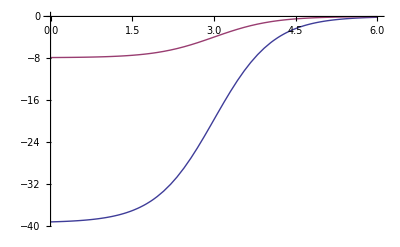

```mathematica
Plot[{Re[V[r]],Im[V[r]]},{r,0,2*R}]
```

## Solve the Schrödinger Equation

First I solve the Schrödinger equation for the radial wavefunction with an arbitrary constant for the initial condition for u'(0). My goal is to show that the resulting phase shift we get from this in independent of the choice of u'(0).

```mathematica
s[L_,k_,b_]:=NDSolve[{u''[r]+(k^2-2*m/(ℏc)^2*V[r]-L*(L+1)/r^2)*u[r]==0,u[(1000*k)^(-1)]==0,u'[(1000*k)^(-1)]==b},u,{r,(1000*k)^(-1),5*R}]
```

```mathematica
u[L_,k_,r_,b_]:=u[r]/.s[L,k,b][[1]]
```

```mathematica
β[L_,k_,b_]:=5*R/Evaluate[u[L,k,5*R,b]]*(D[u[L,k,r,b],r]/.r->(5*R))-1
tanδ[L_,k_,b_]:=N[(k*5*R*Derivative[0,1][SphericalBesselJ][L,k*5*R]-β[L,k,b]*SphericalBesselJ[L,k*5*R])/(k*5*R*Derivative[0,1][SphericalBesselY][L,k*5*R]-β[L,k,b]*SphericalBesselY[L,k*5*R])]
```

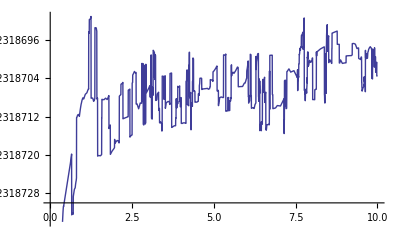

```mathematica
Plot[Re[tanδ[0,1,b]],{b,0.01,10}]
```

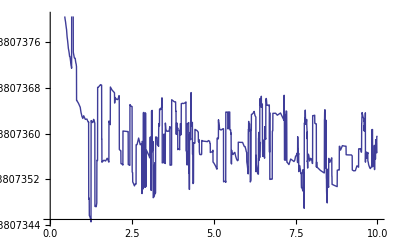

```mathematica
Plot[Im[tanδ[0,1,b]],{b,0.01,10}]
```

As we can see from this plot of tanδ vs. u'(0), the phase shift appears to be independent of our choice of u'(0) up to about 0.01% error.

## Reformulate tanδ for specific choice of u'(0)

These are the same equations as above, but now we have chosen u'(0)=8 (an arbitrary choice).

```mathematica
s[L_,k_]:=NDSolve[{u''[r]+(k^2-2*m/(ℏc)^2*V[r]-L*(L+1)/r^2)*u[r]==0,u[(1000*k)^(-1)]==0,u'[(1000*k)^(-1)]==8},u,{r,(1000*k)^(-1),5*R},MaxSteps->20000]
```

```mathematica
u[L_,k_,r_]:=u[r]/.s[L,k][[1]]
```

```mathematica
β[L_,k_]:=5*R/Evaluate[u[L,k,5*R]]*(D[u[L,k,r],r]/.r->(5*R))-1
tanδ[L_,k_]:=N[(k*5*R*Derivative[0,1][SphericalBesselJ][L,k*5*R]-β[L,k]*SphericalBesselJ[L,k*5*R])/(k*5*R*Derivative[0,1][SphericalBesselY][L,k*5*R]-β[L,k]*SphericalBesselY[L,k*5*R])]
```

```mathematica
Table[tanδ[L,1],{L,0,20}]
```

{-0.923187+0.738074 ⅈ,-1.22237+1.20904 ⅈ,-1.58735+1.99802 ⅈ,1.00564+1.1644 ⅈ,0.211335+0.0713622 ⅈ,0.0403135+0.00963108 ⅈ,0.00812726+0.00172725 ⅈ,0.00165119+0.000337094 ⅈ,0.000333925+0.0000672485 ⅈ,0.0000671337+0.0000134576 ⅈ,0.0000134081+2.6876×10^-6 ⅈ,2.6722×10^-6+5.35051×10^-7 ⅈ,5.30794×10^-7+1.06139×10^-7 ⅈ,1.05238×10^-7+2.09407×10^-8 ⅈ,2.36222×10^-8+4.08615×10^-9 ⅈ,6.62046×10^-9+7.80279×10^-10 ⅈ,1.01519×10^-9+1.43713×10^-10 ⅈ,1.04656×10^-10+2.51393×10^-11 ⅈ,-3.4111×10^-12+4.1209×10^-12 ⅈ,-3.93433×10^-12+6.26806×10^-13 ⅈ,-1.06641×10^-13+8.79197×10^-14 ⅈ}

For k=1, tanδ becomes negligible after about L=5. This is also evident in the plot for continuous L below.

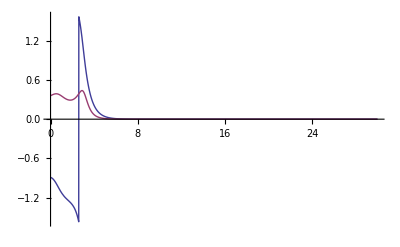

```mathematica
Plot[{Re[ArcTan[tanδ[L,1]]],Im[ArcTan[tanδ[L,1]]]},{L,0,30},PlotRange->{-Pi/2,Pi/2}]
```

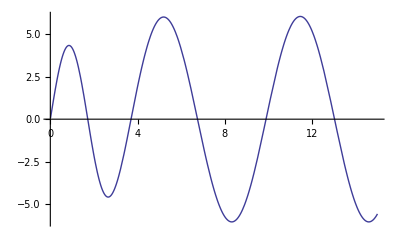

```mathematica
Plot[Evaluate[u[0,1,r]],{r,(100)^(-1),5*R}]
```

Plugging this phase shift into the equations for the scattering amplitude is:

```mathematica
f[k_,θ_]:=1/k*Sum[(2*L+1)*tanδ[L,k]/(1-I*tanδ[L,k])*LegendreP[L,Cos[θ]],{L,0,2*k*R}]
```

Here is a table of some values of dσ/dΩ as a function of θ.

```mathematica
Clear[dσdΩ]
```

```mathematica
dσdΩ[k_,points_:10]:=Table[{θ,Abs[f[k,θ]]^2},{θ,0,Pi,N[1/points]}]
```

```mathematica
dσdΩ[1]
```

```mathematica
{{0.,138.24735648211183},{0.1,131.96418694419444},{0.2,114.6592654903783},{0.30000000000000004,90.39468602293465},{0.4,64.30834749550795},{0.5,40.96502717809941},{0.6000000000000001,23.185107373198356},{0.7000000000000001,11.715122859819573},{0.8,5.663523548401128},{0.9,3.3198513944892047},{1.,2.9319238824176685},{1.1,3.1817325211565817},{1.2000000000000002,3.323652386316457},{1.3,3.0953167489705633},{1.4000000000000001,2.5414915172058445},{1.5,1.8454757211071333},{1.6,1.2047526866685199},{1.7000000000000002,0.7547245075757844},{1.8,0.53626863531564},{1.9000000000000001,0.5023777111949094},{2.,0.5545725801561825},{2.1,0.5922118641706786},{2.2,0.5545270708340819},{2.3000000000000003,0.44029499749236833},{2.4000000000000004,0.3009951398837256},{2.5,0.21397933778536093},{2.6,0.2479553016653255},{2.7,0.43331787347604256},{2.8000000000000003,0.7467074651808787},{2.9000000000000004,1.1146726795353727},{3.,1.4359192277790755},{3.1,1.6154058368157207}}
```

{{0.,138.247},{0.1,131.964},{0.2,114.659},{0.3,90.3947},{0.4,64.3083},{0.5,40.965},{0.6,23.1851},{0.7,11.7151},{0.8,5.66352},{0.9,3.31985},{1.,2.93192},{1.1,3.18173},{1.2,3.32365},{1.3,3.09532},{1.4,2.54149},{1.5,1.84548},{1.6,1.20475},{1.7,0.754725},{1.8,0.536269},{1.9,0.502378},{2.,0.554573},{2.1,0.592212},{2.2,0.554527},{2.3,0.440295},{2.4,0.300995},{2.5,0.213979},{2.6,0.247955},{2.7,0.433318},{2.8,0.746707},{2.9,1.11467},{3.,1.43592},{3.1,1.61541}}

```mathematica
interp1=Interpolation[%]
```

InterpolatingFunction[{{0.,3.1}},<>]

Here is a log plot of that same information.

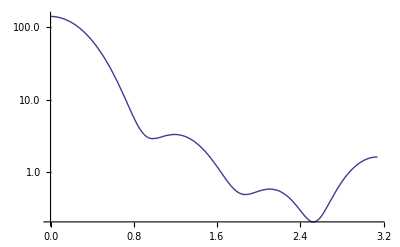

```mathematica
p1=LogPlot[interp1[θ],{θ,0,Pi}]
```

## Eikonal Approximation

These equations come straight out of Sakurai, equations 7.4.13 and 7.4.14 (page 394).

```mathematica
χ0[k_,b_]=-2*m/(k*(ℏc)^2)*NIntegrate[V[Sqrt[b^2+z^2]],{z,0,15}];
T0[k_,b_]:=Exp[I*χ0[k,b]]-1
Eif0[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T0[k,b],{b,0,15}]
```

I had to have the iteration of the table below happen in integer steps because doing it in decimal steps was giving Mathematica problems somehow. I think it probably has something to do with differences in the way it handles integers and floats.

```mathematica
eik0dσdΩ[k_,points_:10]:=Table[{N[θ/points],Abs[Eif0[k,θ/points]]^2},{θ,0,points*Pi,1}]
```

```mathematica
eik0dσdΩ[1]
```

```mathematica
{{0,77.81449298353003},{0.1,74.35383330732927},{0.2,64.84837991679096},{0.30000000000000004,51.57988020244924},{0.4,37.37770256118771},{0.5,24.684171090312795},{0.6000000000000001,14.948965384363145},{0.7000000000000001,8.51791645462917},{0.8,4.915230121696361},{0.9,3.281874841998521},{1.,2.7553515339408743},{1.1,2.6857105335099236},{1.2000000000000002,2.6902902457515094},{1.3,2.6068136696049393},{1.4000000000000001,2.4104679946468877},{1.5,2.1388434537513845},{1.6,1.8425250325094127},{1.7000000000000002,1.5611567627514344},{1.8,1.3170427344045403},{1.9000000000000001,1.1176866720757859},{2.,0.9611434858445198},{2.1,0.8409452369136389},{2.2,0.7494715126304502},{2.3000000000000003,0.6797742195028705},{2.4000000000000004,0.6262920150255549},{2.5,0.5849232679639141},{2.6,0.5528078924322809},{2.7,0.5280292166366286},{2.8000000000000003,0.5093396281148677},{2.9000000000000004,0.4959471492852086},{3.,0.48736597027500483},{3.1,0.48332051398465925}}
```

{{0,77.8145},{0.1,74.3538},{0.2,64.8484},{0.3,51.5799},{0.4,37.3777},{0.5,24.6842},{0.6,14.949},{0.7,8.51792},{0.8,4.91523},{0.9,3.28187},{1.,2.75535},{1.1,2.68571},{1.2,2.69029},{1.3,2.60681},{1.4,2.41047},{1.5,2.13884},{1.6,1.84253},{1.7,1.56116},{1.8,1.31704},{1.9,1.11769},{2.,0.961143},{2.1,0.840945},{2.2,0.749472},{2.3,0.679774},{2.4,0.626292},{2.5,0.584923},{2.6,0.552808},{2.7,0.528029},{2.8,0.50934},{2.9,0.495947},{3.,0.487366},{3.1,0.483321}}

```mathematica
eik0interp1=Interpolation[%]
```

InterpolatingFunction[{{0.,3.1}},<>]

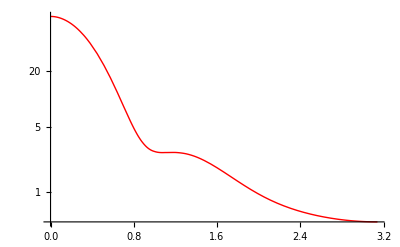

```mathematica
eik0p1=LogPlot[eik0interp1[θ],{θ,0,Pi},PlotStyle->Red]
```

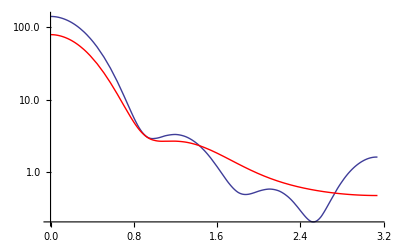

```mathematica
Show[p1,eik0p1]
```

As you can see above, the two plots actually agree with each other pretty well, especially at small θ. There is some pretty obvious disagreement for large θ, however, and the eikonal approximation seems to miss some of the structure apparent in the partial wave formulation.

## Check Method for k=10

For k=10, then k^2 = 100 >> 2*m*V/ℏ^2 ~= -2 - 0.4i, so the eikonal approximation should be valid.

```mathematica
dσdΩ[10]//Timing
```

{510.822,{{0.,486.366},{0.1,13.7655},{0.2,0.142722},{0.3,0.00212583},{0.4,0.000122783},{0.5,1.06992×10^-6},{0.6,3.82125×10^-6},{0.7,1.5606×10^-6},{0.8,9.09828×10^-7},{0.9,4.56746×10^-7},{1.,2.06863×10^-7},{1.1,7.29154×10^-8},{1.2,1.35146×10^-8},{1.3,1.44845×10^-9},{1.4,1.86539×10^-8},{1.5,5.22517×10^-8},{1.6,9.36151×10^-8},{1.7,1.35377×10^-7},{1.8,1.73879×10^-7},{1.9,2.03822×10^-7},{2.,2.24481×10^-7},{2.1,2.3388×10^-7},{2.2,2.31779×10^-7},{2.3,2.17965×10^-7},{2.4,1.94183×10^-7},{2.5,1.61737×10^-7},{2.6,1.23014×10^-7},{2.7,8.11484×10^-8},{2.8,4.02909×10^-8},{2.9,8.73381×10^-9},{3.,6.19344×10^-9},{3.1,1.49821×10^-7}}}

The first number above is the time that command took to evaluate.

```mathematica
interp10=Interpolation[%[[2]]];
```

InterpolatingFunction[{{0.,3.1}},<>]

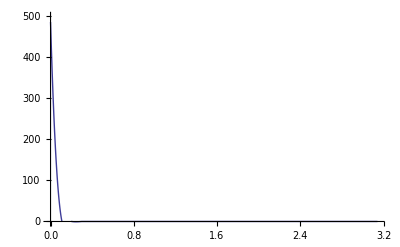

```mathematica
p10=Plot[interp10[θ],{θ,0,Pi},PlotRange->{-1,500}]
```

```mathematica
eik0dσdΩ[10]//Timing
```

{225.703,{{0,486.162},{0.1,14.0605},{0.2,0.13689},{0.3,0.00246745},{0.4,0.0000540022},{0.5,1.42675×10^-6},{0.6,3.23853×10^-8},{0.7,1.29725×10^-9},{0.8,5.91253×10^-11},{0.9,1.26869×10^-11},{1.,8.34575×10^-12},{1.1,3.54278×10^-12},{1.2,2.08122×10^-12},{1.3,1.19259×10^-12},{1.4,7.31612×10^-13},{1.5,4.70504×10^-13},{1.6,3.14678×10^-13},{1.7,2.18652×10^-13},{1.8,1.57428×10^-13},{1.9,1.16839×10^-13},{2.,8.94036×10^-14},{2.1,7.03232×10^-14},{2.2,5.67563×10^-14},{2.3,4.69704×10^-14},{2.4,3.98201×10^-14},{2.5,3.45317×10^-14},{2.6,3.05815×10^-14},{2.7,2.77058×10^-14},{2.8,2.55993×10^-14},{2.9,2.41731×10^-14},{3.,2.32565×10^-14},{3.1,2.28285×10^-14}}}

You can see that as k increases, the eikonal approximation evaluates faster than the partial wave expansion, as we would expect.

```mathematica
eik0interp10=Interpolation[%[[2]]];
```

InterpolatingFunction[{{0.,3.1}},<>]

The points we evaluated dσ/dΩ at are not dense enough to really capture all the detail at small θ, so that's why the plots for k = 10 aren't very good. A better interpolation could be made, but it would take some time.

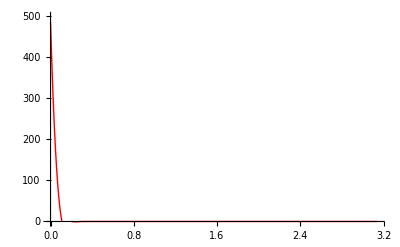

```mathematica
eik0p10=Plot[eik0interp10[θ],{θ,0,Pi},PlotRange->{-1,500},PlotStyle->Red]
```

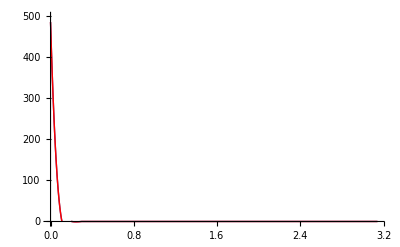

```mathematica
Show[p10,eik0p10]
```

## Plots for k=1,2,3

Partial wave expansion:

```mathematica
dσdΩ[2]
```

```mathematica
{{0.,294.13284672038117},{0.1,254.45387253261455},{0.2,163.58317406315066},{0.30000000000000004,76.44547615877393},{0.4,25.195806907300422},{0.5,6.354727417425964},{0.6000000000000001,2.535031469096774},{0.7000000000000001,2.015320991897528},{0.8,1.3605398752368363},{0.9,0.6475561598926362},{1.,0.246628078993142},{1.1,0.12485882946442764},{1.2000000000000002,0.09728085045525567},{1.3,0.0693530931341297},{1.4000000000000001,0.03991786145950351},{1.5,0.01993961600343463},{1.6,0.0096511939592773},{1.7000000000000002,0.006408061107271777},{1.8,0.005743156089455597},{1.9000000000000001,0.004358759885040449},{2.,0.002756045421293448},{2.1,0.0018200120704008015},{2.2,0.0010261511754880825},{2.3000000000000003,0.00048670218888673464},{2.4000000000000004,0.000452967183570371},{2.5,0.00040782939457310283},{2.6,0.00022484401897185816},{2.7,0.00016598842457262274},{2.8000000000000003,0.00022377492237184296},{2.9000000000000004,0.00016648068861858887},{3.,0.0002458651850978948},{3.1,0.0006132769428460869}}
```

{{0.,294.133},{0.1,254.454},{0.2,163.583},{0.3,76.4455},{0.4,25.1958},{0.5,6.35473},{0.6,2.53503},{0.7,2.01532},{0.8,1.36054},{0.9,0.647556},{1.,0.246628},{1.1,0.124859},{1.2,0.0972809},{1.3,0.0693531},{1.4,0.0399179},{1.5,0.0199396},{1.6,0.00965119},{1.7,0.00640806},{1.8,0.00574316},{1.9,0.00435876},{2.,0.00275605},{2.1,0.00182001},{2.2,0.00102615},{2.3,0.000486702},{2.4,0.000452967},{2.5,0.000407829},{2.6,0.000224844},{2.7,0.000165988},{2.8,0.000223775},{2.9,0.000166481},{3.,0.000245865},{3.1,0.000613277}}

```mathematica
interp2=Interpolation[%];
```

Eikonal approximation

```mathematica
eik0dσdΩ[2]
```

```mathematica
{{0,251.19179243085358},{0.1,218.07823270382934},{0.2,142.43550923869478},{0.30000000000000004,69.6934486158901},{0.4,25.79594241482623},{0.5,8.176606430660355},{0.6000000000000001,3.4487813334198374},{0.7000000000000001,2.259072014984678},{0.8,1.4634079589631463},{0.9,0.7859820236947764},{1.,0.373409682168901},{1.1,0.18633419749197494},{1.2000000000000002,0.11068875336070153},{1.3,0.07274484723353526},{1.4000000000000001,0.046866739068675486},{1.5,0.028506008488484023},{1.6,0.01682654609768932},{1.7000000000000002,0.010176748801496174},{1.8,0.006584627167838333},{1.9000000000000001,0.0045790423329332315},{2.,0.003339103518606545},{2.1,0.0024892062515264844},{2.2,0.001874355372161963},{2.3000000000000003,0.0014254198303045719},{2.4000000000000004,0.0011013153099832431},{2.5,0.0008708836667603661},{2.6,0.0007091916034731125},{2.7,0.000597083415841325},{2.8000000000000003,0.0005206800387014543},{2.9000000000000004,0.0004704737729461426},{3.,0.0004403329543591472},{3.1,0.0004266742238605385}}
```

{{0,251.192},{0.1,218.078},{0.2,142.436},{0.3,69.6934},{0.4,25.7959},{0.5,8.17661},{0.6,3.44878},{0.7,2.25907},{0.8,1.46341},{0.9,0.785982},{1.,0.37341},{1.1,0.186334},{1.2,0.110689},{1.3,0.0727448},{1.4,0.0468667},{1.5,0.028506},{1.6,0.0168265},{1.7,0.0101767},{1.8,0.00658463},{1.9,0.00457904},{2.,0.0033391},{2.1,0.00248921},{2.2,0.00187436},{2.3,0.00142542},{2.4,0.00110132},{2.5,0.000870884},{2.6,0.000709192},{2.7,0.000597083},{2.8,0.00052068},{2.9,0.000470474},{3.,0.000440333},{3.1,0.000426674}}

```mathematica
eik0interp2=Interpolation[%];
```

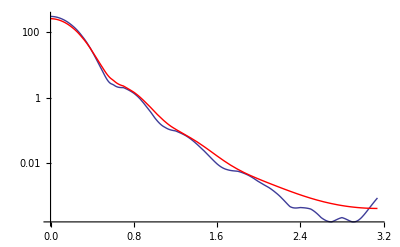

```mathematica
p2=LogPlot[interp2[θ],{θ,0,Pi}];
eik0p2=LogPlot[eik0interp2[θ],{θ,0,Pi},PlotStyle->Red];
Show[p2,eik0p2]
```

Comparison plots: Blue is PWE and red is eikonal

```mathematica
dσdΩ[3,100]
```

```mathematica
{{0.,372.48559843521144},{0.01,371.35582077837626},{0.02,367.98591213208005},{0.03,362.43361691894836},{0.04,354.79343327636053},{0.05,345.19406576953014},{0.06,333.7949892365705},{0.07,320.78224679129715},{0.08,306.3636305472251},{0.09,290.7634126583876},{0.1,274.2168060824059},{0.11,256.96433870964785},{0.12,239.24632119809397},{0.13,221.29757840106197},{0.14,203.3425974029402},{0.15,185.59122289920043},{0.16,168.23500420423264},{0.17,151.44426892329446},{0.18,135.36596772941058},{0.19,120.12230417710443},{0.2,105.81013441033018},{0.21,92.5010951778734},{0.22,80.24239574603997},{0.23,69.05819084188109},{0.24,58.95143815027869},{0.25,49.90613533250107},{0.26,41.88982797761265},{0.27,34.85628104855897},{0.28,28.748211746299667},{0.29,23.499990633886913},{0.3,19.040229574376934},{0.31,15.29418871980617},{0.32,12.185949611880933},{0.33,9.640316623114838},{0.34,7.584423758519316},{0.35000000000000003,5.9490376354105035},{0.36,4.669559769975278},{0.37,3.6867417674213203},{0.38,2.947135419255444},{0.39,2.4033059696800865},{0.4,2.013840955222594},{0.41000000000000003,1.7431891800833812},{0.42,1.5613647759366134},{0.43,1.443550176653851},{0.44,1.369629516193517},{0.45,1.3236807436767672},{0.46,1.2934509479522565},{0.47000000000000003,1.2698352763070204},{0.48,1.2463756654503677},{0.49,1.2187915823895898},{0.5,1.1845512573038364},{0.51,1.1424885926596007},{0.52,1.0924681213892666},{0.53,1.0350980915379184},{0.54,0.971489971833909},{0.55,0.9030613724451946},{0.56,0.8313785090053333},{0.5700000000000001,0.7580338449112684},{0.58,0.6845543599784794},{0.59,0.6123359450815836},{0.6,0.5425996480768045},{0.61,0.47636583817006894},{0.62,0.41444276439964073},{0.63,0.3574264188413403},{0.64,0.30570904585562436},{0.65,0.25949404359022843},{0.66,0.2188153695845073},{0.67,0.18355988214656965},{0.68,0.15349132214727723},{0.6900000000000001,0.12827486901324195},{0.7000000000000001,0.10750139570165525},{0.71,0.09071070743384613},{0.72,0.07741318544654205},{0.73,0.06710937699415398},{0.74,0.05930718218495708},{0.75,0.05353639131702012},{0.76,0.04936042584030609},{0.77,0.04638523284460547},{0.78,0.04426537645539386},{0.79,0.042707457870202845},{0.8,0.041471076300053686},{0.81,0.0403676127026436},{0.8200000000000001,0.039257173857743854},{0.8300000000000001,0.0380440734480785},{0.84,0.03667124757876104},{0.85,0.03511400385086662},{0.86,0.03337348613609433},{0.87,0.03147020320648865},{0.88,0.02943792106565838},{0.89,0.027318159788079867},{0.9,0.025155470066327346},{0.91,0.022993596903938693},{0.92,0.02087257228101049},{0.93,0.018826719032889988},{0.9400000000000001,0.01688349777864136},{0.9500000000000001,0.015063089758413882},{0.96,0.013378582102511409},{0.97,0.011836608532098307},{0.98,0.010438296988741755},{0.99,0.009180384604750166},{1.,0.00805637756125657},{1.01,0.007057656192043033},{1.02,0.006174451541508079},{1.03,0.005396645981379177},{1.04,0.004714375277958436},{1.05,0.004118431004440003},{1.06,0.0036004792925349647},{1.07,0.0031531240663327594},{1.08,0.002769850078383985},{1.09,0.002444883691387763},{1.1,0.002173008156718682},{1.11,0.0019493660602480727},{1.12,0.0017692756243731394},{1.1300000000000001,0.0016280806110744504},{1.1400000000000001,0.0015210464691956828},{1.1500000000000001,0.0014433087305125208},{1.16,0.0013898739009681662},{1.17,0.0013556684402536714},{1.18,0.0013356279384136422},{1.19,0.0013248162301793909},{1.2,0.0013185628167942643},{1.21,0.0013126064483245255},{1.22,0.001303232923503582},{1.23,0.0012873959836958964},{1.24,0.0012628115386470427},{1.25,0.0012280173123252122},{1.26,0.0011823922892948567},{1.27,0.0011261330104162367},{1.28,0.001060186710154892},{1.29,0.0009861443583503546},{1.3,0.0009060996713693038},{1.31,0.000822482859387167},{1.32,0.0007378800321536823},{1.33,0.0006548505644951809},{1.34,0.0005757551425658785},{1.35,0.0005026065684535078},{1.36,0.00043695369133330757},{1.37,0.00037980616736930337},{1.3800000000000001,0.00033160434642468965},{1.3900000000000001,0.00029223475078872085},{1.4000000000000001,0.00026108771883321855},{1.41,0.00023715022332339804},{1.42,0.0002191240029614654},{1.43,0.00020555726063936915},{1.44,0.00019497747193450101},{1.45,0.00018601337311844406},{1.46,0.0001774958831391544},{1.47,0.00016853035435928214},{1.48,0.00015853583432574343},{1.49,0.00014725058108671697},{1.5,0.00013470651180569375},{1.51,0.0001211782088350583},{1.52,0.00010711425851794784},{1.53,0.00009305985863188746},{1.54,0.00007957972720014331},{1.55,0.0000671894333170896},{1.56,0.00005630152130156313},{1.57,0.00004719047535855743},{1.58,0.000039977989820132596},{1.59,0.00003463749915677574},{1.6,0.00003101478195988745},{1.61,0.000028859917691475737},{1.62,0.000027865085585095717},{1.6300000000000001,0.00002770268763478344},{1.6400000000000001,0.000028058983952986727},{1.6500000000000001,0.00002865969159799955},{1.6600000000000001,0.000029285596987054356},{1.67,0.000029777917376458103},{1.68,0.000030034674997545797},{1.69,0.00003000051416109338},{1.7,0.00002965305856162347},{1.71,0.000028989016267181087},{1.72,0.0000280128218612256},{1.73,0.00002672976401818231},{1.74,0.000025144445148334987},{1.75,0.00002326425132832284},{1.76,0.00002110647012475224},{1.77,0.000018706947463533445},{1.78,0.000016127836458692465},{1.79,0.00001346210724925678},{1.8,0.000010833030487754764},{1.81,8.387723975044961*^-6},{1.82,6.284916195739405*^-6},{1.83,4.678157719118203*^-6},{1.84,3.6966254506985223*^-6},{1.85,3.426264551912158*^-6},{1.86,3.894195444905701*^-6},{1.87,5.0590391063352425*^-6},{1.8800000000000001,6.80911273535266*^-6},{1.8900000000000001,8.9694149897671*^-6},{1.9000000000000001,0.000011317101823087194},{1.9100000000000001,0.000013603927011550142},{1.92,0.000015583066426769602},{1.93,0.000017037020448112953},{1.94,0.000017803007576848883},{1.95,0.00001779247499697787},{1.96,0.000017002039078409787},{1.97,0.00001551424323168149},{1.98,0.000013487838632209338},{1.99,0.000011138675543031588},{2.,8.713548703810178*^-6},{2.0100000000000002,6.460294765123297*^-6},{2.02,4.5979587559497715*^-6},{2.0300000000000002,3.2908553305351813*^-6},{2.04,2.6298445629503573*^-6},{2.05,2.623188034832123*^-6},{2.06,3.1980777129496814*^-6},{2.07,4.2125108382522045*^-6},{2.08,5.4758123596350195*^-6},{2.09,6.7749695322668556*^-6},{2.1,7.903195966359099*^-6},{2.11,8.686885619918205*^-6},{2.12,9.007384134793048*^-6},{2.13,8.814756343084641*^-6},{2.14,8.131858750631302*^-6},{2.15,7.048376394969571*^-6},{2.16,5.7058668031747385*^-6},{2.17,4.276078208903303*^-6},{2.18,2.935706000436732*^-6},{2.19,1.841198171752516*^-6},{2.2,1.107158220561352*^-6},{2.21,7.913347264236452*^-7},{2.22,8.882124684000331*^-7},{2.23,1.331970005902322*^-6},{2.24,2.0082209526706945*^-6},{2.25,2.772701718520258*^-6},{2.2600000000000002,3.4740846163313995*^-6},{2.27,3.977520683570779*^-6},{2.2800000000000002,4.185431986640666*^-6},{2.29,4.052489712402391*^-6},{2.3000000000000003,3.5925720448706456*^-6},{2.31,2.876671986386848*^-6},{2.32,2.0220517200466413*^-6},{2.33,1.1742268153289276*^-6},{2.34,4.844255657380409*^-7},{2.35,8.585228943251741*^-8},{2.36,7.228800231301097*^-8},{2.37,4.822547316363079*^-7},{2.38,1.2911909613548464*^-6},{2.39,2.412943043761477*^-6},{2.4,3.710531545800438*^-6},{2.41,5.014793667701734*^-6},{2.42,6.148328054550349*^-6},{2.43,6.95134761694427*^-6},{2.44,7.3057020927414975*^-6},{2.45,7.153521390560012*^-6},{2.46,6.507634503057843*^-6},{2.47,5.452044769210439*^-6},{2.48,4.13213691029074*^-6},{2.49,2.7357604125846705*^-6},{2.5,1.4676695810729294*^-6},{2.5100000000000002,5.208104071222691*^-7},{2.52,4.8478485116143336*^-8},{2.5300000000000002,1.4134531331533932*^-7},{2.54,8.127547714005154*^-7},{2.5500000000000003,1.9945997698843382*^-6},{2.56,3.544644716859317*^-6},{2.57,5.264558724797492*^-6},{2.58,6.926389555132142*^-6},{2.59,8.303956754488011*^-6},{2.6,9.204856774458567*^-6},{2.61,9.49857432316909*^-6},{2.62,9.136624578026558*^-6},{2.63,8.16166507884078*^-6},{2.64,6.703986488585644*^-6},{2.65,4.965523737700429*^-6},{2.66,3.1932880138387553*^-6},{2.67,1.6456608354262394*^-6},{2.68,5.56093484721685*^-7},{2.69,9.925308289560981*^-8},{2.7,3.64464697425034*^-7},{2.71,1.3404244146083759*^-6},{2.72,2.9137031331473918*^-6},{2.73,4.881709692680517*^-6},{2.74,6.978779289554525*^-6},{2.75,8.9121711642763*^-6},{2.7600000000000002,0.000010403261765487463},{2.77,0.000011228324576729575},{2.7800000000000002,0.000011253138176989718},{2.79,0.000010456305099724037},{2.8000000000000003,8.937534546697356*^-6},{2.81,6.9090798119076985*^-6},{2.82,4.670782088729556*^-6},{2.83,2.5714602945622093*^-6},{2.84,9.613924199123116*^-7},{2.85,1.4207613964856493*^-7},{2.86,3.201195815841302*^-7},{2.87,1.5718786042569881*^-6},{2.88,3.824321541218456*^-6},{2.89,6.855682356298148*^-6},{2.9,0.000010316982415442605},{2.91,0.000013772764983353086},{2.92,0.000016756744388143218},{2.93,0.000018835872506926302},{2.94,0.000019674872024768812},{2.95,0.00001909279568992618},{2.96,0.00001710374360833591},{2.97,0.000013935473597804738},{2.98,0.000010022107417245834},{2.99,5.970188000563847*^-6},{3.,2.5006169708188494*^-6},{3.0100000000000002,3.720963807029831*^-7},{3.02,2.942235120794289*^-7},{3.0300000000000002,2.840012614038088*^-6},{3.04,8.368115515569546*^-6},{3.0500000000000003,0.00001696429040354368},{3.06,0.00002840977882042796},{3.0700000000000003,0.00004218139321122315},{3.08,0.00005748461141424541},{3.09,0.00007331722548945961},{3.1,0.00008855754188693112},{3.11,0.00010206820293179878},{3.12,0.00011280475180059937},{3.13,0.00011991733752385703},{3.14,0.0001228345525346104}}
```

{{0.,372.486},{0.01,371.356},{0.02,367.986},{0.03,362.434},{0.04,354.793},{0.05,345.194},{0.06,333.795},{0.07,320.782},{0.08,306.364},{0.09,290.763},{0.1,274.217},{0.11,256.964},{0.12,239.246},{0.13,221.298},{0.14,203.343},{0.15,185.591},{0.16,168.235},{0.17,151.444},{0.18,135.366},{0.19,120.122},{0.2,105.81},{0.21,92.5011},{0.22,80.2424},{0.23,69.0582},{0.24,58.9514},{0.25,49.9061},{0.26,41.8898},{0.27,34.8563},{0.28,28.7482},{0.29,23.5},{0.3,19.0402},{0.31,15.2942},{0.32,12.1859},{0.33,9.64032},{0.34,7.58442},{0.35,5.94904},{0.36,4.66956},{0.37,3.68674},{0.38,2.94714},{0.39,2.40331},{0.4,2.01384},{0.41,1.74319},{0.42,1.56136},{0.43,1.44355},{0.44,1.36963},{0.45,1.32368},{0.46,1.29345},{0.47,1.26984},{0.48,1.24638},{0.49,1.21879},{0.5,1.18455},{0.51,1.14249},{0.52,1.09247},{0.53,1.0351},{0.54,0.97149},{0.55,0.903061},{0.56,0.831379},{0.57,0.758034},{0.58,0.684554},{0.59,0.612336},{0.6,0.5426},{0.61,0.476366},{0.62,0.414443},{0.63,0.357426},{0.64,0.305709},{0.65,0.259494},{0.66,0.218815},{0.67,0.18356},{0.68,0.153491},{0.69,0.128275},{0.7,0.107501},{0.71,0.0907107},{0.72,0.0774132},{0.73,0.0671094},{0.74,0.0593072},{0.75,0.0535364},{0.76,0.0493604},{0.77,0.0463852},{0.78,0.0442654},{0.79,0.0427075},{0.8,0.0414711},{0.81,0.0403676},{0.82,0.0392572},{0.83,0.0380441},{0.84,0.0366712},{0.85,0.035114},{0.86,0.0333735},{0.87,0.0314702},{0.88,0.0294379},{0.89,0.0273182},{0.9,0.0251555},{0.91,0.0229936},{0.92,0.0208726},{0.93,0.0188267},{0.94,0.0168835},{0.95,0.0150631},{0.96,0.0133786},{0.97,0.0118366},{0.98,0.0104383},{0.99,0.00918038},{1.,0.00805638},{1.01,0.00705766},{1.02,0.00617445},{1.03,0.00539665},{1.04,0.00471438},{1.05,0.00411843},{1.06,0.00360048},{1.07,0.00315312},{1.08,0.00276985},{1.09,0.00244488},{1.1,0.00217301},{1.11,0.00194937},{1.12,0.00176928},{1.13,0.00162808},{1.14,0.00152105},{1.15,0.00144331},{1.16,0.00138987},{1.17,0.00135567},{1.18,0.00133563},{1.19,0.00132482},{1.2,0.00131856},{1.21,0.00131261},{1.22,0.00130323},{1.23,0.0012874},{1.24,0.00126281},{1.25,0.00122802},{1.26,0.00118239},{1.27,0.00112613},{1.28,0.00106019},{1.29,0.000986144},{1.3,0.0009061},{1.31,0.000822483},{1.32,0.00073788},{1.33,0.000654851},{1.34,0.000575755},{1.35,0.000502607},{1.36,0.000436954},{1.37,0.000379806},{1.38,0.000331604},{1.39,0.000292235},{1.4,0.000261088},{1.41,0.00023715},{1.42,0.000219124},{1.43,0.000205557},{1.44,0.000194977},{1.45,0.000186013},{1.46,0.000177496},{1.47,0.00016853},{1.48,0.000158536},{1.49,0.000147251},{1.5,0.000134707},{1.51,0.000121178},{1.52,0.000107114},{1.53,0.0000930599},{1.54,0.0000795797},{1.55,0.0000671894},{1.56,0.0000563015},{1.57,0.0000471905},{1.58,0.000039978},{1.59,0.0000346375},{1.6,0.0000310148},{1.61,0.0000288599},{1.62,0.0000278651},{1.63,0.0000277027},{1.64,0.000028059},{1.65,0.0000286597},{1.66,0.0000292856},{1.67,0.0000297779},{1.68,0.0000300347},{1.69,0.0000300005},{1.7,0.0000296531},{1.71,0.000028989},{1.72,0.0000280128},{1.73,0.0000267298},{1.74,0.0000251444},{1.75,0.0000232643},{1.76,0.0000211065},{1.77,0.0000187069},{1.78,0.0000161278},{1.79,0.0000134621},{1.8,0.000010833},{1.81,8.38772×10^-6},{1.82,6.28492×10^-6},{1.83,4.67816×10^-6},{1.84,3.69663×10^-6},{1.85,3.42626×10^-6},{1.86,3.8942×10^-6},{1.87,5.05904×10^-6},{1.88,6.80911×10^-6},{1.89,8.96941×10^-6},{1.9,0.0000113171},{1.91,0.0000136039},{1.92,0.0000155831},{1.93,0.000017037},{1.94,0.000017803},{1.95,0.0000177925},{1.96,0.000017002},{1.97,0.0000155142},{1.98,0.0000134878},{1.99,0.0000111387},{2.,8.71355×10^-6},{2.01,6.46029×10^-6},{2.02,4.59796×10^-6},{2.03,3.29086×10^-6},{2.04,2.62984×10^-6},{2.05,2.62319×10^-6},{2.06,3.19808×10^-6},{2.07,4.21251×10^-6},{2.08,5.47581×10^-6},{2.09,6.77497×10^-6},{2.1,7.9032×10^-6},{2.11,8.68689×10^-6},{2.12,9.00738×10^-6},{2.13,8.81476×10^-6},{2.14,8.13186×10^-6},{2.15,7.04838×10^-6},{2.16,5.70587×10^-6},{2.17,4.27608×10^-6},{2.18,2.93571×10^-6},{2.19,1.8412×10^-6},{2.2,1.10716×10^-6},{2.21,7.91335×10^-7},{2.22,8.88212×10^-7},{2.23,1.33197×10^-6},{2.24,2.00822×10^-6},{2.25,2.7727×10^-6},{2.26,3.47408×10^-6},{2.27,3.97752×10^-6},{2.28,4.18543×10^-6},{2.29,4.05249×10^-6},{2.3,3.59257×10^-6},{2.31,2.87667×10^-6},{2.32,2.02205×10^-6},{2.33,1.17423×10^-6},{2.34,4.84426×10^-7},{2.35,8.58523×10^-8},{2.36,7.2288×10^-8},{2.37,4.82255×10^-7},{2.38,1.29119×10^-6},{2.39,2.41294×10^-6},{2.4,3.71053×10^-6},{2.41,5.01479×10^-6},{2.42,6.14833×10^-6},{2.43,6.95135×10^-6},{2.44,7.3057×10^-6},{2.45,7.15352×10^-6},{2.46,6.50763×10^-6},{2.47,5.45204×10^-6},{2.48,4.13214×10^-6},{2.49,2.73576×10^-6},{2.5,1.46767×10^-6},{2.51,5.2081×10^-7},{2.52,4.84785×10^-8},{2.53,1.41345×10^-7},{2.54,8.12755×10^-7},{2.55,1.9946×10^-6},{2.56,3.54464×10^-6},{2.57,5.26456×10^-6},{2.58,6.92639×10^-6},{2.59,8.30396×10^-6},{2.6,9.20486×10^-6},{2.61,9.49857×10^-6},{2.62,9.13662×10^-6},{2.63,8.16167×10^-6},{2.64,6.70399×10^-6},{2.65,4.96552×10^-6},{2.66,3.19329×10^-6},{2.67,1.64566×10^-6},{2.68,5.56093×10^-7},{2.69,9.92531×10^-8},{2.7,3.64465×10^-7},{2.71,1.34042×10^-6},{2.72,2.9137×10^-6},{2.73,4.88171×10^-6},{2.74,6.97878×10^-6},{2.75,8.91217×10^-6},{2.76,0.0000104033},{2.77,0.0000112283},{2.78,0.0000112531},{2.79,0.0000104563},{2.8,8.93753×10^-6},{2.81,6.90908×10^-6},{2.82,4.67078×10^-6},{2.83,2.57146×10^-6},{2.84,9.61392×10^-7},{2.85,1.42076×10^-7},{2.86,3.2012×10^-7},{2.87,1.57188×10^-6},{2.88,3.82432×10^-6},{2.89,6.85568×10^-6},{2.9,0.000010317},{2.91,0.0000137728},{2.92,0.0000167567},{2.93,0.0000188359},{2.94,0.0000196749},{2.95,0.0000190928},{2.96,0.0000171037},{2.97,0.0000139355},{2.98,0.0000100221},{2.99,5.97019×10^-6},{3.,2.50062×10^-6},{3.01,3.72096×10^-7},{3.02,2.94224×10^-7},{3.03,2.84001×10^-6},{3.04,8.36812×10^-6},{3.05,0.0000169643},{3.06,0.0000284098},{3.07,0.0000421814},{3.08,0.0000574846},{3.09,0.0000733172},{3.1,0.0000885575},{3.11,0.000102068},{3.12,0.000112805},{3.13,0.000119917},{3.14,0.000122835}}

```mathematica
temp=Interpolation[%]
```

InterpolatingFunction[{{0.,3.14}},<>]

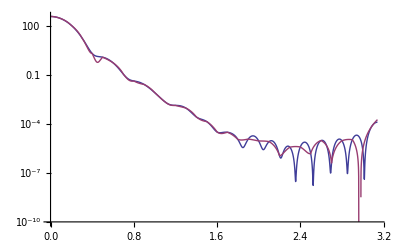

```mathematica
LogPlot[{temp[θ],interp3[θ]},{θ,0,Pi}]
```

Plot comparing interpolation made using points spaced in steps of 0.1 (purple), and points spaced in steps of 0.01 (blue). There is significant structure missed as θ becomes larger than π/2 (albeit the magnitude there is very small), but more importantly, there is a defect in the differential scattering cross-section near θ = 0.5 in the 0.1 interpolation that is fixed by moving to the higher density of interpolation points. From now on, we will calculate differential cross-sections with k ≥ 3 with a higher density of interpolation points.

```mathematica
interp3=Interpolation[dσdΩ[3]];
```

```mathematica
eik0dσdΩ[3,100]
```

```mathematica
{{0.,349.768368649314},{0.01,348.71478343926736},{0.02,345.5725311128451},{0.03,340.3965890229478},{0.04,333.2768323706189},{0.05,324.3354776500099},{0.06,313.72364752141806},{0.07,301.6171920959797},{0.08,288.2119279014283},{0.09,273.7184739891927},{0.1,258.3568740681287},{0.11,242.35119407152453},{0.12,225.92427656237143},{0.13,209.29281770558717},{0.14,192.66291041995672},{0.15,176.22617028585987},{0.16,160.1565305146801},{0.17,144.60776052011911},{0.18,129.71173104771776},{0.19,115.57741893636576},{0.2,102.29061768963389},{0.21,89.91429712282623},{0.22,78.4895371051176},{0.23,68.03694719578878},{0.24,58.55847583635002},{0.25,50.03950949393807},{0.26,42.45116331783386},{0.27,35.75266986972978},{0.28,29.893780595421884},{0.29,24.817105153550237},{0.3,20.46032572102192},{0.31,16.7582362130365},{0.32,13.644569314824972},{0.33,11.053586744630161},{0.34,8.92141978540834},{0.35,7.187157484712375},{0.36,5.793688791460146},{0.37,4.6883121449513885},{0.38,3.823131622340242},{0.39,3.155262728396838},{0.4,2.646873390797921},{0.41,2.2650868551843484},{0.42,1.9817731496518316},{0.43,1.7732548088251354},{0.44,1.6199508219581875},{0.45,1.5059804984827878},{0.46,1.4187463148695565},{0.47,1.3485119852658107},{0.48,1.2879891281411553},{0.49,1.2319431007478698},{0.5,1.1768259314261826},{0.51,1.120441872758531},{0.52,1.061648959244789},{0.53,1.0000981197482177},{0.54,0.9360098675301258},{0.55,0.8699873677537107},{0.56,0.8028637469542966},{0.57,0.7355808373428857},{0.58,0.6690961117370626},{0.59,0.6043143301954386},{0.6,0.5420403537957126},{0.61,0.48294965165426457},{0.62,0.4275732031389386},{0.63,0.376293749749188},{0.64,0.3293506549427512},{0.65,0.286850963361999},{0.66,0.2487845951237589},{0.67,0.21504195127249337},{0.68,0.1854325316860248},{0.69,0.15970346824518136},{0.7,0.1375571482304622},{0.71,0.11866734232392909},{0.72,0.10269345686668237},{0.73,0.08929270132146348},{0.74,0.07813010061308977},{0.75,0.06888639046311285},{0.76,0.061263914909059566},{0.77,0.05499070217861627},{0.78,0.04982293141099244},{0.79,0.04554602181101849},{0.8,0.04197458098167667},{0.81,0.038951443471925654},{0.82,0.03634601677649218},{0.83,0.03405213256534814},{0.84,0.03198557790531717},{0.85,0.030081456401127277},{0.86,0.028291503940715532},{0.87,0.026581459177017718},{0.88,0.024928565831017473},{0.89,0.02331926292602019},{0.9,0.021747100516678844},{0.91,0.020210902535106805},{0.92,0.018713185076943216},{0.93,0.017258827713997137},{0.94,0.015853987091525853},{0.95,0.014505235927719424},{0.96,0.013218906328288533},{0.97,0.012000613807745069},{0.98,0.010854937246757262},{0.99,0.009785230040173384},{1.,0.008793538542709076},{1.01,0.00788060546634172},{1.02,0.007045937872228339},{1.03,0.00628792167653553},{1.04,0.005603967006544036},{1.05,0.004990671181632534},{1.06,0.004443988462170411},{1.07,0.0039593979407901905},{1.08,0.0035320629693633794},{1.09,0.003156977398327633},{1.1,0.0028290953847049127},{1.11,0.0025434429726800263},{1.12,0.00229521069820784},{1.13,0.00207982737666935},{1.14,0.0018930159124405767},{1.15,0.0017308324689567884},{1.16,0.0015896906763710975},{1.17,0.0014663727651197968},{1.18,0.0013580295785664332},{1.19,0.001262171457752636},{1.2,0.0011766518769910693},{1.21,0.0010996456087688823},{1.22,0.0010296230262050385},{1.23,0.0009653219678764185},{1.24,0.0009057183940512918},{1.25,0.0008499968656297853},{1.26,0.0007975216850222375},{1.27,0.0007478093569865428},{1.28,0.0007005028613365564},{1.29,0.0006553480807765395},{1.3,0.0006121725972038828},{1.31,0.0005708669594783454},{1.32,0.0005313684338484606},{1.33,0.0004936471748177642},{1.34,0.00045769469718441976},{1.35,0.00042351448826597545},{1.36,0.00039111457061667335},{1.37,0.0003605018085546781},{1.38,0.0003316777442411247},{1.39,0.0003046357493974858},{1.4,0.0002793592854556591},{1.41,0.0002558210761265157},{1.42,0.00023398301126167594},{1.43,0.0002137966177862861},{1.44,0.00019520395183869426},{1.45,0.0001781387849977099},{1.46,0.00016252797598992905},{1.47,0.0001482929371947048},{1.48,0.00013535112200066123},{1.49,0.00012361747440455768},{1.5,0.00011300579628061113},{1.51,0.00010342999979094365},{1.52,0.00009480522322214128},{1.53,0.00008704879740421565},{1.54,0.00008008105737425237},{1.55,0.00007382600004720842},{1.56,0.00006821179329405276},{1.57,0.0000631711454752824},{1.58,0.000058641546992232274},{1.59,0.000054565397068062665},{1.6,0.00005089002992494559},{1.61,0.00004756765479233054},{1.62,0.000044555224017976284},{1.63,0.00004181424297949443},{1.64,0.0000393105346352172},{1.65,0.000037013970512133365},{1.66,0.00003489817872096269},{1.67,0.000032940238370649276},{1.68,0.000031120368459422776},{1.69,0.0000294216180866786},{1.7,0.000027829563640549894},{1.71,0.000026332017477950437},{1.72,0.00002491875161838147},{1.73,0.000023581239015318703},{1.74,0.000022312414171633786},{1.75,0.000021106454143038823},{1.76,0.00001995858036904242},{1.77,0.000018864881263740013},{1.78,0.000017822155084852397},{1.79,0.00001682777227743475},{1.8,0.000015879556233139238},{1.81,0.000014975681233383507},{1.82,0.000014114586220949607},{1.83,0.000013294902982733662},{1.84,0.00001251539729248948},{1.85,0.000011774921588548777},{1.86,0.000011072377784121392},{1.87,0.000010406688886549953},{1.88,9.776778168132561*^-6},{1.89,9.181554725931955*^-6},{1.9,8.619904368397752*^-6},{1.91,8.090684858847759*^-6},{1.92,7.592724658990548*^-6},{1.93,7.124824403532605*^-6},{1.94,6.685760444766783*^-6},{1.95,6.2742898876372225*^-6},{1.96,5.8891566321766924*^-6},{1.97,5.529098007806144*^-6},{1.98,5.192851663303283*^-6},{1.99,4.87916244353531*^-6},{2.,4.586789031269313*^-6},{2.01,4.31451019392233*^-6},{2.02,4.061130515469883*^-6},{2.03,3.825485525665452*^-6},{2.04,3.6064461826398838*^-6},{2.05,3.4029226806489845*^-6},{2.06,3.2138675788247426*^-6},{2.07,3.0382782713594264*^-6},{2.08,2.8751988228294445*^-6},{2.09,2.7237212072493964*^-6},{2.1,2.582985998240354*^-6},{2.11,2.45218256029062*^-6},{2.12,2.3305487915598024*^-6},{2.13,2.2173704765377653*^-6},{2.14,2.111980295741302*^-6},{2.15,2.013756550809472*^-6},{2.16,1.9221216496203295*^-6},{2.17,1.8365404002311728*^-6},{2.18,1.7565181547667573*^-6},{2.19,1.6815988456646073*^-6},{2.2,1.6113629452251745*^-6},{2.21,1.5454253843528898*^-6},{2.22,1.4834334546924711*^-6},{2.23,1.4250647210435768*^-6},{2.24,1.3700249620806542*^-6},{2.25,1.3180461583824886*^-6},{2.26,1.268884540904261*^-6},{2.27,1.2223187117432711*^-6},{2.28,1.1781478455392765*^-6},{2.29,1.136189978701781*^-6},{2.3,1.0962803901602762*^-6},{2.31,1.058270077224248*^-6},{2.32,1.0220243270783105*^-6},{2.33,9.874213842635189*^-7},{2.34,9.543512128121894*^-7},{2.35,9.227143508163292*^-7},{2.36,8.924208549540998*^-7},{2.37,8.633893311078528*^-7},{2.38,8.355460477051663*^-7},{2.39,8.088241269458187*^-7},{2.4,7.831628102670898*^-7},{2.41,7.585067928725815*^-7},{2.42,7.348056231534497*^-7},{2.43,7.120131621595333*^-7},{2.44,6.900870988236854*^-7},{2.45,6.689885164300461*^-7},{2.46,6.486815061726454*^-7},{2.47,6.291328236775136*^-7},{2.48,6.103115847319267*^-7},{2.49,5.921889963863014*^-7},{2.5,5.747381203407031*^-7},{2.51,5.579336649511143*^-7},{2.52,5.417518033351236*^-7},{2.53,5.261700145525827*^-7},{2.54,5.111669453478052*^-7},{2.55,4.967222902489343*^-7},{2.56,4.828166878787136*^-7},{2.57,4.694316313139083*^-7},{2.58,4.5654939116060196*^-7},{2.59,4.4415294939404266*^-7},{2.6,4.3222594270715186*^-7},{2.61,4.207526142471726*^-7},{2.62,4.097177722086441*^-7},{2.63,3.9910675473158814*^-7},{2.64,3.8890539992164235*^-7},{2.65,3.791000203089813*^-7},{2.66,3.6967738100390296*^-7},{2.67,3.606246811007126*^-7},{2.68,3.519295180636558*^-7},{2.69,3.43579972175837*^-7},{2.7,3.3556439761792667*^-7},{2.71,3.2787160876517594*^-7},{2.72,3.2049077241799205*^-7},{2.73,3.1341141894385274*^-7},{2.74,3.066234345184946*^-7},{2.75,3.0011705386606855*^-7},{2.76,2.9388285370349936*^-7},{2.77,2.879117462712034*^-7},{2.78,2.82194973109923*^-7},{2.79,2.767240989374553*^-7},{2.8,2.7149100619745905*^-7},{2.81,2.6648788871117385*^-7},{2.82,2.617072462923205*^-7},{2.83,2.571418788293361*^-7},{2.84,2.5278488065267556*^-7},{2.85,2.4862963482101847*^-7},{2.86,2.4466980727867375*^-7},{2.87,2.40899341525468*^-7},{2.88,2.3731245267121816*^-7},{2.89,2.3390362195033542*^-7},{2.9,2.306675911815322*^-7},{2.91,2.2759935730535365*^-7},{2.92,2.2469416694401174*^-7},{2.93,2.219475111468024*^-7},{2.94,2.1935512015365885*^-7},{2.95,2.1691295832542398*^-7},{2.96,2.14617219405332*^-7},{2.97,2.1246432148362346*^-7},{2.98,2.104509025244162*^-7},{2.99,2.0857381601408628*^-7},{3.,2.068301266379763*^-7},{3.01,2.0521710627839317*^-7},{3.02,2.037322302467065*^-7},{3.03,2.023731737226453*^-7},{3.04,2.0113780823076026*^-7},{3.05,2.0002419885586842*^-7},{3.06,1.9903060095134975*^-7},{3.07,1.9815545781941648*^-7},{3.08,1.9739739840011514*^-7},{3.09,1.9675523483563018*^-7},{3.1,1.962279609897484*^-7},{3.11,1.9581475073150097*^-7},{3.12,1.9551495656278395*^-7},{3.13,1.9532810881687024*^-7},{3.14,1.952539146961793*^-7}}
```

{{0.,349.768},{0.01,348.715},{0.02,345.573},{0.03,340.397},{0.04,333.277},{0.05,324.335},{0.06,313.724},{0.07,301.617},{0.08,288.212},{0.09,273.718},{0.1,258.357},{0.11,242.351},{0.12,225.924},{0.13,209.293},{0.14,192.663},{0.15,176.226},{0.16,160.157},{0.17,144.608},{0.18,129.712},{0.19,115.577},{0.2,102.291},{0.21,89.9143},{0.22,78.4895},{0.23,68.0369},{0.24,58.5585},{0.25,50.0395},{0.26,42.4512},{0.27,35.7527},{0.28,29.8938},{0.29,24.8171},{0.3,20.4603},{0.31,16.7582},{0.32,13.6446},{0.33,11.0536},{0.34,8.92142},{0.35,7.18716},{0.36,5.79369},{0.37,4.68831},{0.38,3.82313},{0.39,3.15526},{0.4,2.64687},{0.41,2.26509},{0.42,1.98177},{0.43,1.77325},{0.44,1.61995},{0.45,1.50598},{0.46,1.41875},{0.47,1.34851},{0.48,1.28799},{0.49,1.23194},{0.5,1.17683},{0.51,1.12044},{0.52,1.06165},{0.53,1.0001},{0.54,0.93601},{0.55,0.869987},{0.56,0.802864},{0.57,0.735581},{0.58,0.669096},{0.59,0.604314},{0.6,0.54204},{0.61,0.48295},{0.62,0.427573},{0.63,0.376294},{0.64,0.329351},{0.65,0.286851},{0.66,0.248785},{0.67,0.215042},{0.68,0.185433},{0.69,0.159703},{0.7,0.137557},{0.71,0.118667},{0.72,0.102693},{0.73,0.0892927},{0.74,0.0781301},{0.75,0.0688864},{0.76,0.0612639},{0.77,0.0549907},{0.78,0.0498229},{0.79,0.045546},{0.8,0.0419746},{0.81,0.0389514},{0.82,0.036346},{0.83,0.0340521},{0.84,0.0319856},{0.85,0.0300815},{0.86,0.0282915},{0.87,0.0265815},{0.88,0.0249286},{0.89,0.0233193},{0.9,0.0217471},{0.91,0.0202109},{0.92,0.0187132},{0.93,0.0172588},{0.94,0.015854},{0.95,0.0145052},{0.96,0.0132189},{0.97,0.0120006},{0.98,0.0108549},{0.99,0.00978523},{1.,0.00879354},{1.01,0.00788061},{1.02,0.00704594},{1.03,0.00628792},{1.04,0.00560397},{1.05,0.00499067},{1.06,0.00444399},{1.07,0.0039594},{1.08,0.00353206},{1.09,0.00315698},{1.1,0.0028291},{1.11,0.00254344},{1.12,0.00229521},{1.13,0.00207983},{1.14,0.00189302},{1.15,0.00173083},{1.16,0.00158969},{1.17,0.00146637},{1.18,0.00135803},{1.19,0.00126217},{1.2,0.00117665},{1.21,0.00109965},{1.22,0.00102962},{1.23,0.000965322},{1.24,0.000905718},{1.25,0.000849997},{1.26,0.000797522},{1.27,0.000747809},{1.28,0.000700503},{1.29,0.000655348},{1.3,0.000612173},{1.31,0.000570867},{1.32,0.000531368},{1.33,0.000493647},{1.34,0.000457695},{1.35,0.000423514},{1.36,0.000391115},{1.37,0.000360502},{1.38,0.000331678},{1.39,0.000304636},{1.4,0.000279359},{1.41,0.000255821},{1.42,0.000233983},{1.43,0.000213797},{1.44,0.000195204},{1.45,0.000178139},{1.46,0.000162528},{1.47,0.000148293},{1.48,0.000135351},{1.49,0.000123617},{1.5,0.000113006},{1.51,0.00010343},{1.52,0.0000948052},{1.53,0.0000870488},{1.54,0.0000800811},{1.55,0.000073826},{1.56,0.0000682118},{1.57,0.0000631711},{1.58,0.0000586415},{1.59,0.0000545654},{1.6,0.00005089},{1.61,0.0000475677},{1.62,0.0000445552},{1.63,0.0000418142},{1.64,0.0000393105},{1.65,0.000037014},{1.66,0.0000348982},{1.67,0.0000329402},{1.68,0.0000311204},{1.69,0.0000294216},{1.7,0.0000278296},{1.71,0.000026332},{1.72,0.0000249188},{1.73,0.0000235812},{1.74,0.0000223124},{1.75,0.0000211065},{1.76,0.0000199586},{1.77,0.0000188649},{1.78,0.0000178222},{1.79,0.0000168278},{1.8,0.0000158796},{1.81,0.0000149757},{1.82,0.0000141146},{1.83,0.0000132949},{1.84,0.0000125154},{1.85,0.0000117749},{1.86,0.0000110724},{1.87,0.0000104067},{1.88,9.77678×10^-6},{1.89,9.18155×10^-6},{1.9,8.6199×10^-6},{1.91,8.09068×10^-6},{1.92,7.59272×10^-6},{1.93,7.12482×10^-6},{1.94,6.68576×10^-6},{1.95,6.27429×10^-6},{1.96,5.88916×10^-6},{1.97,5.5291×10^-6},{1.98,5.19285×10^-6},{1.99,4.87916×10^-6},{2.,4.58679×10^-6},{2.01,4.31451×10^-6},{2.02,4.06113×10^-6},{2.03,3.82549×10^-6},{2.04,3.60645×10^-6},{2.05,3.40292×10^-6},{2.06,3.21387×10^-6},{2.07,3.03828×10^-6},{2.08,2.8752×10^-6},{2.09,2.72372×10^-6},{2.1,2.58299×10^-6},{2.11,2.45218×10^-6},{2.12,2.33055×10^-6},{2.13,2.21737×10^-6},{2.14,2.11198×10^-6},{2.15,2.01376×10^-6},{2.16,1.92212×10^-6},{2.17,1.83654×10^-6},{2.18,1.75652×10^-6},{2.19,1.6816×10^-6},{2.2,1.61136×10^-6},{2.21,1.54543×10^-6},{2.22,1.48343×10^-6},{2.23,1.42506×10^-6},{2.24,1.37002×10^-6},{2.25,1.31805×10^-6},{2.26,1.26888×10^-6},{2.27,1.22232×10^-6},{2.28,1.17815×10^-6},{2.29,1.13619×10^-6},{2.3,1.09628×10^-6},{2.31,1.05827×10^-6},{2.32,1.02202×10^-6},{2.33,9.87421×10^-7},{2.34,9.54351×10^-7},{2.35,9.22714×10^-7},{2.36,8.92421×10^-7},{2.37,8.63389×10^-7},{2.38,8.35546×10^-7},{2.39,8.08824×10^-7},{2.4,7.83163×10^-7},{2.41,7.58507×10^-7},{2.42,7.34806×10^-7},{2.43,7.12013×10^-7},{2.44,6.90087×10^-7},{2.45,6.68989×10^-7},{2.46,6.48682×10^-7},{2.47,6.29133×10^-7},{2.48,6.10312×10^-7},{2.49,5.92189×10^-7},{2.5,5.74738×10^-7},{2.51,5.57934×10^-7},{2.52,5.41752×10^-7},{2.53,5.2617×10^-7},{2.54,5.11167×10^-7},{2.55,4.96722×10^-7},{2.56,4.82817×10^-7},{2.57,4.69432×10^-7},{2.58,4.56549×10^-7},{2.59,4.44153×10^-7},{2.6,4.32226×10^-7},{2.61,4.20753×10^-7},{2.62,4.09718×10^-7},{2.63,3.99107×10^-7},{2.64,3.88905×10^-7},{2.65,3.791×10^-7},{2.66,3.69677×10^-7},{2.67,3.60625×10^-7},{2.68,3.5193×10^-7},{2.69,3.4358×10^-7},{2.7,3.35564×10^-7},{2.71,3.27872×10^-7},{2.72,3.20491×10^-7},{2.73,3.13411×10^-7},{2.74,3.06623×10^-7},{2.75,3.00117×10^-7},{2.76,2.93883×10^-7},{2.77,2.87912×10^-7},{2.78,2.82195×10^-7},{2.79,2.76724×10^-7},{2.8,2.71491×10^-7},{2.81,2.66488×10^-7},{2.82,2.61707×10^-7},{2.83,2.57142×10^-7},{2.84,2.52785×10^-7},{2.85,2.4863×10^-7},{2.86,2.4467×10^-7},{2.87,2.40899×10^-7},{2.88,2.37312×10^-7},{2.89,2.33904×10^-7},{2.9,2.30668×10^-7},{2.91,2.27599×10^-7},{2.92,2.24694×10^-7},{2.93,2.21948×10^-7},{2.94,2.19355×10^-7},{2.95,2.16913×10^-7},{2.96,2.14617×10^-7},{2.97,2.12464×10^-7},{2.98,2.10451×10^-7},{2.99,2.08574×10^-7},{3.,2.0683×10^-7},{3.01,2.05217×10^-7},{3.02,2.03732×10^-7},{3.03,2.02373×10^-7},{3.04,2.01138×10^-7},{3.05,2.00024×10^-7},{3.06,1.99031×10^-7},{3.07,1.98155×10^-7},{3.08,1.97397×10^-7},{3.09,1.96755×10^-7},{3.1,1.96228×10^-7},{3.11,1.95815×10^-7},{3.12,1.95515×10^-7},{3.13,1.95328×10^-7},{3.14,1.95254×10^-7}}

```mathematica
eik0interp3=Interpolation[%];
```

```mathematica
eik0p3=LogPlot[eik0interp3[θ],{θ,0,Pi},PlotStyle->Red];
```

```mathematica
LogPlot[{temp[θ],eik0interp3[θ]},{θ,0,Pi}];
```

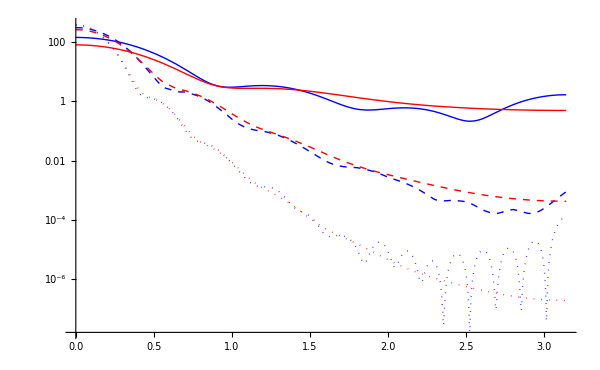

```mathematica
LogPlot[{interp1[θ],eik0interp1[θ],interp2[θ],eik0interp2[θ],temp[θ],eik0interp3[θ]},{θ,0,Pi},PlotStyle->{{Blue},{Red},{Blue,Dashed},{Red,Dashed},{Blue,Dotted},{Red,Dotted}},PlotLegend->{"Partial Wave: k=1","Eikonal: k=1","Partial Wave: k=2","Eikonal: k=2","Partial Wave: k=3","Eikonal: k=3"},LegendPosition->{1.1,-0.4},LegendSize->{1,1},ImageSize->600]
```

The eikonal approximation actually appears to track the partial wave expansion quite well for k = 1, 2, and 3, but is again missing a lot of the finer structure.

## Plot for k=0.1

As you can see below, the approximation gets pretty bad as k -> 0.

```mathematica
Abs[f[.1,0]]^2
```

9.73572

```mathematica
Abs[Eif0[.1,0]]^2
```

2.19448

```mathematica
interp01=Interpolation[dσdΩ[.1]];
eik0interp01=Interpolation[eik0dσdΩ[.1]];
```

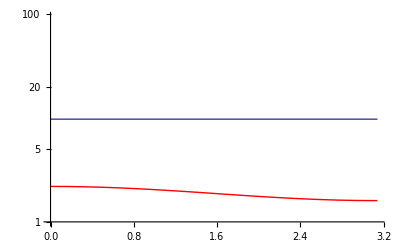

```mathematica
p01=LogPlot[interp01[θ],{θ,0,Pi}];
eik0p01=LogPlot[eik0interp01[θ],{θ,0,Pi},PlotStyle->Red];
Show[p01,eik0p01]
```

## Add in Eikonal Corrections

### First order correction

Below are parameters used by Wallace in his treatment of this:

```mathematica
En[k_]:=(k*ℏc)^2/(2*m)
U[r_]:=V[r]/V0
ϵ[k_]:=V0/(2*En[k])
```

```mathematica
τ1[k_,b_]=-k*ϵ[k]^2*NIntegrate[Evaluate[(1#+b*D[#,b])&[U[Sqrt[z^2+b^2]]^2]],{z,0,15}];
```

```mathematica
T1[k_,b_]:=Exp[I(χ0[k,b]+τ1[k,b])]-1
Eif1[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T1[k,b],{b,0,15}]
```

```mathematica
eik1dσdΩ[k_,points_:10]:=Table[{N[θ/points],Abs[Eif1[k,θ/points]]^2},{θ,0,points*Pi,1}]
```

```mathematica
eik1dσdΩ[1]
```

```mathematica
{{0,95.4916407772874},{0.1,91.32199667027986},{0.2,79.86029789021228},{0.30000000000000004,63.83251860614333},{0.4,46.61806047886127},{0.5,31.13218458477662},{0.6000000000000001,19.10343172145061},{0.7000000000000001,10.945660308418605},{0.8,6.103142092341639},{0.9,3.5805588439806946},{1.,2.396007663282738},{1.1,1.8297781203824133},{1.2000000000000002,1.475354223042364},{1.3,1.1702049267435877},{1.4000000000000001,0.8900373371639697},{1.5,0.6606109499365427},{1.6,0.5064375376323211},{1.7000000000000002,0.4323783941693593},{1.8,0.42510355033326486},{1.9000000000000001,0.462055380077732},{2.,0.5201768131124003},{2.1,0.5812761228251279},{2.2,0.633878093546306},{2.3000000000000003,0.6726887783467668},{2.4000000000000004,0.6969557306764929},{2.5,0.7086561077676782},{2.6,0.7110054139349729},{2.7,0.7074417226557099},{2.8000000000000003,0.7010463606139952},{2.9000000000000004,0.6942840274609752},{3.,0.6889372825388839},{3.1,0.6861339763325287}}
```

{{0,95.4916},{0.1,91.322},{0.2,79.8603},{0.3,63.8325},{0.4,46.6181},{0.5,31.1322},{0.6,19.1034},{0.7,10.9457},{0.8,6.10314},{0.9,3.58056},{1.,2.39601},{1.1,1.82978},{1.2,1.47535},{1.3,1.1702},{1.4,0.890037},{1.5,0.660611},{1.6,0.506438},{1.7,0.432378},{1.8,0.425104},{1.9,0.462055},{2.,0.520177},{2.1,0.581276},{2.2,0.633878},{2.3,0.672689},{2.4,0.696956},{2.5,0.708656},{2.6,0.711005},{2.7,0.707442},{2.8,0.701046},{2.9,0.694284},{3.,0.688937},{3.1,0.686134}}

```mathematica
eik1interp1=Interpolation[%];
```

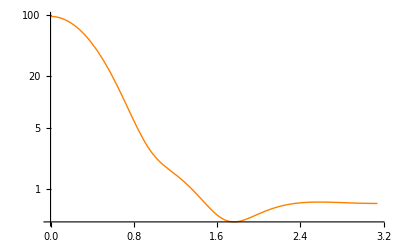

```mathematica
eik1p1=LogPlot[eik1interp1[θ],{θ,0,Pi},PlotStyle->Orange]
```

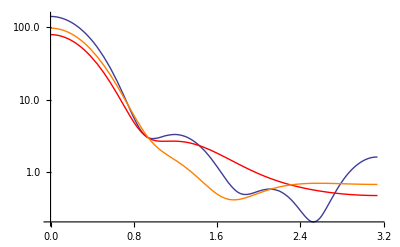

```mathematica
Show[p1,eik0p1,eik1p1]
```

### Second order correction

```mathematica
τ2[k_,b_]=-k*ϵ[k]^3*NIntegrate[Evaluate[(1#+5/3*b*D[#,b]+1/3*b^2*D[#,{b,2}])&[U[Sqrt[z^2+b^2]]^3]],{z,0,15}]-b*D[χ0[k,b],b]^3/(24*k^2);
ω2[k_,b_]=D[χ0[k,b],b]*D[b*D[χ0[k,b],b],b]/(8*k^2);
```

```mathematica
T2[k_,b_]:=Exp[I(χ0[k,b]+τ1[k,b]+τ2[k,b])]*Exp[-ω2[k,b]]-1
Eif2[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T2[k,b],{b,0,15}]
```

```mathematica
eik2dσdΩ[k_,points_:10]:=Table[{N[θ/points],Abs[Eif2[k,θ/points]]^2},{θ,0,points*Pi,1}]
```

```mathematica
eik2dσdΩ[1]
```

```mathematica
{{0,112.03119082261938},{0.1,106.89568506829538},{0.2,92.7953798404284},{0.30000000000000004,73.13051106162756},{0.4,52.11581348586382},{0.5,33.38355595493003},{0.6000000000000001,19.07736041694531},{0.7000000000000001,9.688510308007045},{0.8,4.485719199536133},{0.9,2.1794807983848976},{1.,1.4930808395446646},{1.1,1.4799197453987092},{1.2000000000000002,1.5939397365928438},{1.3,1.6088442190260712},{1.4000000000000001,1.4893376265574616},{1.5,1.280933914937446},{1.6,1.042321696860511},{1.7000000000000002,0.8162811636562891},{1.8,0.6246040803759986},{1.9000000000000001,0.4733412847329669},{2.,0.3598653324624358},{2.1,0.27814786026616284},{2.2,0.22166471514522806},{2.3000000000000003,0.1845741749606819},{2.4000000000000004,0.16198244958124203},{2.5,0.14986546263140724},{2.6,0.1449299610951089},{2.7,0.14450681031135076},{2.8000000000000003,0.14648148606675424},{2.9000000000000004,0.14924379388332837},{3.,0.15164387015524086},{3.1,0.15295213172349517}}
```

{{0,112.031},{0.1,106.896},{0.2,92.7954},{0.3,73.1305},{0.4,52.1158},{0.5,33.3836},{0.6,19.0774},{0.7,9.68851},{0.8,4.48572},{0.9,2.17948},{1.,1.49308},{1.1,1.47992},{1.2,1.59394},{1.3,1.60884},{1.4,1.48934},{1.5,1.28093},{1.6,1.04232},{1.7,0.816281},{1.8,0.624604},{1.9,0.473341},{2.,0.359865},{2.1,0.278148},{2.2,0.221665},{2.3,0.184574},{2.4,0.161982},{2.5,0.149865},{2.6,0.14493},{2.7,0.144507},{2.8,0.146481},{2.9,0.149244},{3.,0.151644},{3.1,0.152952}}

```mathematica
eik2interp1=Interpolation[%];
```

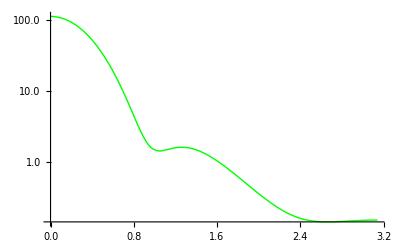

```mathematica
eik2p1=LogPlot[eik2interp1[θ],{θ,0,Pi},PlotStyle->Green]
```

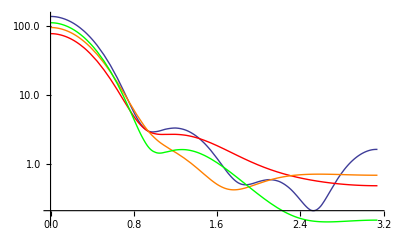

```mathematica
Show[p1,eik0p1,eik1p1,eik2p1,PlotRange->Automatic]
```

### Third order correction

```mathematica
τ3[k_,b_]=-k*ϵ[k]^4*NIntegrate[Evaluate[(5/4#+11/4*b*D[#,b]+b^2*D[#,{b,2}]+1/12*b^3*D[#,{b,3}])&[U[Sqrt[z^2+b^2]]^4]],{z,0,15}]-b*D[τ1[k,b],b]*D[χ0[k,b],b]^2/(8*k^2);
ϕ3[k_,b_]=-k*ϵ[k]^2*NIntegrate[Evaluate[(1#+5/3*b*D[#,b]+1/3*b^2*D[#,{b,2}])&[(1/(2*k)*D[U[Sqrt[z^2+b^2]],b])^2]],{z,0,15}];
ω3[k_,b_]=(D[χ0[k,b],b]*D[b*D[τ1[k,b],b],b]+D[τ1[k,b],b]*D[b*D[χ0[k,b],b],b])/(8*k^2);
```

```mathematica
T3[k_,b_]:=Exp[I*(χ0[k,b]+τ1[k,b]+τ2[k,b]+τ3[k,b]+ϕ3[k,b])]*Exp[-(ω2[k,b]+ω3[k,b])]-1
```

```mathematica
Eif3[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T3[k,b],{b,0,15}]
```

```mathematica
eik3dσdΩ[k_,points_:10]:=Table[{N[θ/points],Abs[Eif3[k,θ/points]]^2},{θ,0,points*Pi,1}]
```

```mathematica
eik3dσdΩ[1]
```

```mathematica
{{0,91.44454627711006},{0.1,86.93401462142639},{0.2,74.63539942644337},{0.30000000000000004,57.73580994872822},{0.4,40.1191611488699},{0.5,25.01154909387827},{0.6000000000000001,14.137423616688872},{0.7000000000000001,7.628404129429616},{0.8,4.517113985599908},{0.9,3.4373177523439993},{1.,3.191026845603401},{1.1,3.025041125904266},{1.2000000000000002,2.6393069732410597},{1.3,2.04368047822072},{1.4000000000000001,1.3836954073218313},{1.5,0.8100455864643781},{1.6,0.41410762975043075},{1.7000000000000002,0.21737791131140125},{1.8,0.19041266794593914},{1.9000000000000001,0.27971259914912966},{2.,0.4297942445530772},{2.1,0.5960371098986682},{2.2,0.7491310507723384},{2.3000000000000003,0.8740401298795031},{2.4000000000000004,0.966433394680398},{2.5,1.028668140282196},{2.6,1.066427761430172},{2.7,1.0863750659977414},{2.8000000000000003,1.0947558839109996},{2.9000000000000004,1.0967122891307253},{3.,1.096041229838605},{3.1,1.0951810613831496}}
```

{{0,91.4445},{0.1,86.934},{0.2,74.6354},{0.3,57.7358},{0.4,40.1192},{0.5,25.0115},{0.6,14.1374},{0.7,7.6284},{0.8,4.51711},{0.9,3.43732},{1.,3.19103},{1.1,3.02504},{1.2,2.63931},{1.3,2.04368},{1.4,1.3837},{1.5,0.810046},{1.6,0.414108},{1.7,0.217378},{1.8,0.190413},{1.9,0.279713},{2.,0.429794},{2.1,0.596037},{2.2,0.749131},{2.3,0.87404},{2.4,0.966433},{2.5,1.02867},{2.6,1.06643},{2.7,1.08638},{2.8,1.09476},{2.9,1.09671},{3.,1.09604},{3.1,1.09518}}

```mathematica
eik3interp1=Interpolation[%];
```

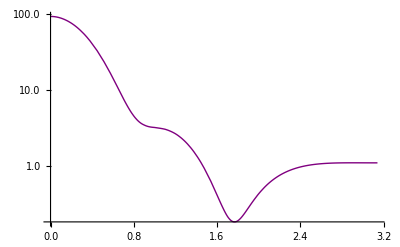

```mathematica
eik3p1=LogPlot[eik3interp1[θ],{θ,0,Pi},PlotStyle->Purple]
```

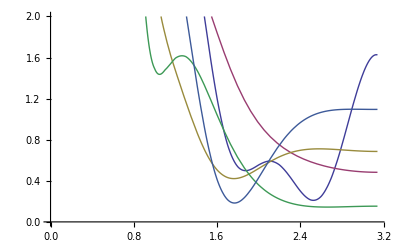

```mathematica
Plot[{interp1[θ],eik0interp1[θ],eik1interp1[θ],eik2interp1[θ],eik3interp1[θ]},{θ,0,π},PlotRange->{0,2}]
```

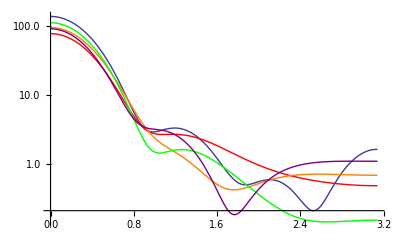

```mathematica
Show[p1,eik0p1,eik1p1,eik2p1,eik3p1,PlotRange->Automatic]
```

### Eikonal to third order for k = 1, 2, 3

```mathematica
eik1dσdΩ[2]
```

```mathematica
{{0,293.22916757681776},{0.1,253.73708442891774},{0.2,163.54525083771438},{0.30000000000000004,77.12185874818907},{0.4,25.827549639078388},{0.5,6.470193765582039},{0.6000000000000001,2.404829314396261},{0.7000000000000001,1.9708446558230917},{0.8,1.4418483020129758},{0.9,0.7725091233405128},{1.,0.3469346095016307},{1.1,0.17920260076861255},{1.2000000000000002,0.12740509798030303},{1.3,0.09836042734065897},{1.4000000000000001,0.06913635577519377},{1.5,0.044201145819914786},{1.6,0.027723797564798387},{1.7000000000000002,0.01858997815221487},{1.8,0.01371874720343962},{1.9000000000000001,0.010736034325405947},{2.,0.00851044754298138},{2.1,0.0066970413471289306},{2.2,0.005241989043030437},{2.3000000000000003,0.004130130923060545},{2.4000000000000004,0.003317940686099176},{2.5,0.0027421904266382103},{2.6,0.0023402945942820387},{2.7,0.0020618251899269546},{2.8000000000000003,0.0018709300822241403},{2.9000000000000004,0.0017441597963126962},{3.,0.0016671795249573332},{3.1,0.0016319996781983062}}
```

{{0,293.229},{0.1,253.737},{0.2,163.545},{0.3,77.1219},{0.4,25.8275},{0.5,6.47019},{0.6,2.40483},{0.7,1.97084},{0.8,1.44185},{0.9,0.772509},{1.,0.346935},{1.1,0.179203},{1.2,0.127405},{1.3,0.0983604},{1.4,0.0691364},{1.5,0.0442011},{1.6,0.0277238},{1.7,0.01859},{1.8,0.0137187},{1.9,0.010736},{2.,0.00851045},{2.1,0.00669704},{2.2,0.00524199},{2.3,0.00413013},{2.4,0.00331794},{2.5,0.00274219},{2.6,0.00234029},{2.7,0.00206183},{2.8,0.00187093},{2.9,0.00174416},{3.,0.00166718},{3.1,0.001632}}

```mathematica
eik1interp2=Interpolation[%];
```

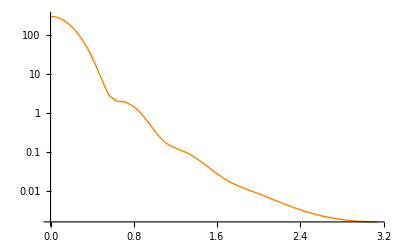

```mathematica
eik1p2=LogPlot[eik1interp2[θ],{θ,0,Pi},PlotStyle->Orange]
```

```mathematica
eik2dσdΩ[2]
```

```mathematica
{{0,294.8910610420141},{0.1,254.64906314911445},{0.2,163.0438766536933},{0.30000000000000004,75.93509962321531},{0.4,24.995469770821455},{0.5,6.304885592324231},{0.6000000000000001,2.5700573876368416},{0.7000000000000001,2.0945827457899067},{0.8,1.4219824225411097},{0.9,0.684685732267747},{1.,0.2732260646789869},{1.1,0.14396253329387548},{1.2000000000000002,0.1179262007797158},{1.3,0.09744344816721406},{1.4000000000000001,0.0684080785672247},{1.5,0.04267666743910603},{1.6,0.026908537622400235},{1.7000000000000002,0.019553362451643495},{1.8,0.01646813408118401},{1.9000000000000001,0.014645895152346293},{2.,0.012856322382081679},{2.1,0.01094820113938691},{2.2,0.009122353927508044},{2.3000000000000003,0.007560083105323252},{2.4000000000000004,0.006329439588063352},{2.5,0.005411916311465128},{2.6,0.004750752991457766},{2.7,0.004284532348888232},{2.8000000000000003,0.003962528625692157},{2.9000000000000004,0.0037483595712716152},{3.,0.0036184361539684435},{3.1,0.0035591384191706516}}
```

{{0,294.891},{0.1,254.649},{0.2,163.044},{0.3,75.9351},{0.4,24.9955},{0.5,6.30489},{0.6,2.57006},{0.7,2.09458},{0.8,1.42198},{0.9,0.684686},{1.,0.273226},{1.1,0.143963},{1.2,0.117926},{1.3,0.0974434},{1.4,0.0684081},{1.5,0.0426767},{1.6,0.0269085},{1.7,0.0195534},{1.8,0.0164681},{1.9,0.0146459},{2.,0.0128563},{2.1,0.0109482},{2.2,0.00912235},{2.3,0.00756008},{2.4,0.00632944},{2.5,0.00541192},{2.6,0.00475075},{2.7,0.00428453},{2.8,0.00396253},{2.9,0.00374836},{3.,0.00361844},{3.1,0.00355914}}

```mathematica
eik2interp2=Interpolation[%];
```

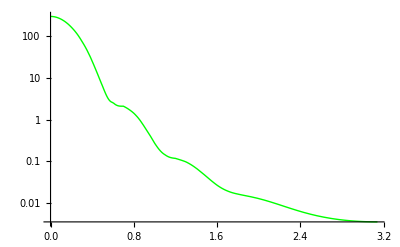

```mathematica
eik2p2=LogPlot[eik2interp2[θ],{θ,0,Pi},PlotStyle->Green]
```

```mathematica
eik3dσdΩ[2]
```

```mathematica
{{0,294.86691456514865},{0.1,254.72568209257432},{0.2,163.3026128276939},{0.30000000000000004,76.26132870351331},{0.4,25.23290700858881},{0.5,6.396043386339652},{0.6000000000000001,2.5518405487150866},{0.7000000000000001,2.031782755927383},{0.8,1.3639402190579146},{0.9,0.6519501171856685},{1.,0.26136665900409967},{1.1,0.13815228081376424},{1.2000000000000002,0.10790737102051179},{1.3,0.08268003362366579},{1.4000000000000001,0.053761303230222456},{1.5,0.032256482613916955},{1.6,0.021524363471284717},{1.7000000000000002,0.017681889654967888},{1.8,0.01617669761158569},{1.9000000000000001,0.014717166618473682},{2.,0.012906519213103873},{2.1,0.011067812566862553},{2.2,0.009514511180635484},{2.3000000000000003,0.008353938975641188},{2.4000000000000004,0.007544120654285952},{2.5,0.0069908764873193785},{2.6,0.006607264957444925},{2.7,0.006333323810317747},{2.8000000000000003,0.00613449966297479},{2.9000000000000004,0.005993551971246569},{3.,0.005903002447388051},{3.1,0.005860089596276548}}
```

{{0,294.867},{0.1,254.726},{0.2,163.303},{0.3,76.2613},{0.4,25.2329},{0.5,6.39604},{0.6,2.55184},{0.7,2.03178},{0.8,1.36394},{0.9,0.65195},{1.,0.261367},{1.1,0.138152},{1.2,0.107907},{1.3,0.08268},{1.4,0.0537613},{1.5,0.0322565},{1.6,0.0215244},{1.7,0.0176819},{1.8,0.0161767},{1.9,0.0147172},{2.,0.0129065},{2.1,0.0110678},{2.2,0.00951451},{2.3,0.00835394},{2.4,0.00754412},{2.5,0.00699088},{2.6,0.00660726},{2.7,0.00633332},{2.8,0.0061345},{2.9,0.00599355},{3.,0.005903},{3.1,0.00586009}}

```mathematica
eik3interp2=Interpolation[%];
```

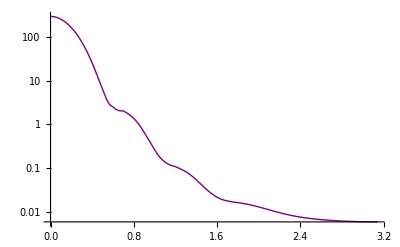

```mathematica
eik3p2=LogPlot[eik3interp2[θ],{θ,0,Pi},PlotStyle->Purple]
```

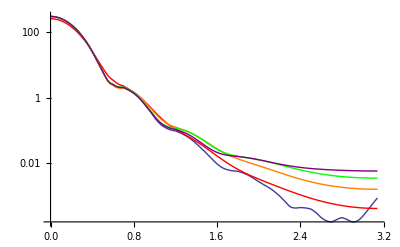

```mathematica
Show[p2,eik0p2,eik1p2,eik2p2,eik3p2,PlotRange->Automatic]
```

```mathematica
eik1dσdΩ[3,100]
```

```mathematica
{{0.,374.13781381048307},{0.01,372.9924352365846},{0.02,369.5764944900654},{0.03,363.94999741306157},{0.04,356.2110466279768},{0.05,346.4930607284497},{0.06,334.96103659736303},{0.07,321.80700061346386},{0.08,307.24482302297866},{0.09,291.50458960011684},{0.1,274.82673516963416},{0.11,257.45614445108004},{0.12,239.6364173953523},{0.13,221.6044796065673},{0.14,203.58569487788586},{0.15,185.78960792767757},{0.16,168.4064128968459},{0.17,151.6042089149153},{0.18,135.52706986015446},{0.19,120.29392296554035},{0.2,105.99820155234163},{0.21,92.70821199963676},{0.22,80.46813484073157},{0.23,69.29956503526144},{0.24,59.203487093034816},{0.25,50.162576626469686},{0.26,42.143720642228345},{0.27,35.10065382731625},{0.28,28.97661648296383},{0.29,23.706950795770805},{0.3,19.221564971846327},{0.31,15.44720859514822},{0.32,12.309516672785195},{0.33,9.734793561826066},{0.34,7.651520812372226},{0.35,5.991584510657416},{0.36,4.691227686393697},{0.37,3.691741597780101},{0.38,2.9399161685463358},{0.39,2.3882745513509676},{0.4,1.9951198370331393},{0.41,1.7244234705083015},{0.42,1.5455851685966986},{0.43,1.433093274959512},{0.44,1.3661127556954116},{0.45,1.32802565436674},{0.46,1.3059459930934698},{0.47,1.2902280132581372},{0.48,1.273983457849327},{0.49,1.252620443791906},{0.5,1.2234134659928246},{0.51,1.185111298096398},{0.52,1.1375870661985075},{0.53,1.0815326068528885},{0.54,1.0181973960965458},{0.55,0.9491708522420836},{0.56,0.8762056590503844},{0.57,0.8010789053633993},{0.58,0.7254872622200904},{0.59,0.6509720856036946},{0.6,0.5788702055676518},{0.61,0.5102862042913494},{0.62,0.4460821611474568},{0.63,0.38688111898197636},{0.64,0.3330808724171769},{0.65,0.2848750695543306},{0.66,0.2422790302746418},{0.67,0.20515809859611783},{0.68,0.17325674821330506},{0.69,0.14622703795249603},{0.7,0.12365535918915212},{0.71,0.1050867249365385},{0.72,0.09004611743494878},{0.73,0.07805663681438461},{0.74,0.0686543785924728},{0.75,0.06140011450413567},{0.76,0.05588796247212293},{0.77,0.05175131107633176},{0.78,0.048666315682653546},{0.79,0.04635331160570944},{0.8,0.04457649842034246},{0.81,0.04314224273393081},{0.82,0.04189632804472823},{0.83,0.04072045301591003},{0.84,0.03952824650641681},{0.85,0.03826103147644478},{0.86,0.03688353249704382},{0.87,0.03537968469075286},{0.88,0.03374866679545727},{0.89,0.03200124861326495},{0.9,0.030156514017714797},{0.91,0.02823899531988171},{0.92,0.02627623329659005},{0.93,0.02429675954015907},{0.94,0.022328483845796464},{0.95,0.020397458845633525},{0.96,0.018526986697175844},{0.97,0.01673702798124516},{0.98,0.015043870611082113},{0.99,0.013460016200984457},{1.,0.011994242487147167},{1.01,0.010651802773902999},{1.02,0.00943472661169807},{1.03,0.008342189727633243},{1.04,0.007370925371520464},{1.05,0.006515653497712485},{1.06,0.005769508405782452},{1.07,0.005124449482044743},{1.08,0.00457164336777611},{1.09,0.004101809367571587},{1.1,0.0037055226730064073},{1.11,0.003373472725044936},{1.12,0.0030966760385517885},{1.13,0.0028666445673546873},{1.14,0.0026755120128801524},{1.15,0.002516121459262672},{1.16,0.002382078384975052},{1.17,0.0022677734956340406},{1.18,0.0021683799947550425},{1.19,0.002079829866296656},{1.2,0.0019987736029421924},{1.21,0.0019225274935317342},{1.22,0.0018490122354803114},{1.23,0.001776686210261392},{1.24,0.0017044763124666972},{1.25,0.0016317087664055126},{1.26,0.001558041917243974},{1.27,0.0014834025581129092},{1.28,0.0014079269608863294},{1.29,0.0013319074229608627},{1.3,0.00125574482826694},{1.31,0.001179907451888439},{1.32,0.0011048960114723064},{1.33,0.0010312147860155215},{1.34,0.0009593484793300845},{1.35,0.0008897443994958891},{1.36,0.0008227994520112325},{1.37,0.0007588514000881523},{1.38,0.000698173825452878},{1.39,0.0006409742235693248},{1.4,0.0005873946843521528},{1.41,0.0005375146390759511},{1.42,0.0004913551936413724},{1.43,0.00044888461389927303},{1.44,0.00041002457839715964},{1.45,0.0003746568650888102},{1.46,0.00034263018950239687},{1.47,0.00031376696134726546},{1.48,0.0002878697731002793},{1.49,0.00026472747711808704},{1.5,0.0002441207468333636},{1.51,0.00022582705188706483},{1.52,0.0002096250070472521},{1.53,0.000195298079948174},{1.54,0.00018263766361696762},{1.55,0.00017144553654395317},{1.56,0.00016153574591318997},{1.57,0.00015273595916029061},{1.58,0.00014488833543288378},{1.59,0.00013784997233661647},{1.6,0.00013149298492851834},{1.61,0.00012570427358040584},{1.62,0.00012038503565684614},{1.63,0.00011545007291079895},{1.64,0.00011082694280896875},{1.65,0.00010645499758575926},{1.66,0.00010228435013598425},{1.67,0.00009827480093362979},{1.68,0.00009439475531884178},{1.69,0.00009062015572720753},{1.7,0.00008693344890793408},{1.71,0.00008332260397502475},{1.72,0.00007978019327799979},{1.73,0.00007630254461065219},{1.74,0.00007288897024033877},{1.75,0.00006954107557468509},{1.76,0.00006626214805464615},{1.77,0.00006305662501261661},{1.78,0.000059929637719374393},{1.79,0.00005688662769544341},{1.8,0.00005393303045770977},{1.81,0.000051074021319344144},{1.82,0.00004831431742963491},{1.83,0.000045658030105031},{1.84,0.00004310856145087499},{1.85,0.00004066853943945167},{1.86,0.0000383397857852157},{1.87,0.000036123311322701796},{1.88,0.00003401933391993781},{1.89,0.00003202731439733517},{1.9,0.000030146006355326973},{1.91,0.00002837351624143235},{1.92,0.00002670737046360616},{1.93,0.000025144586748307942},{1.94,0.000023681747391665144},{1.95,0.000022315072412021223},{1.96,0.00002104049099582404},{1.97,0.000019853709934064645},{1.98,0.00001875027805781317},{1.99,0.000017725645947207206},{2.,0.000016775220400778822},{2.01,0.000015894413372095567},{2.02,0.000015078685237040635},{2.03,0.00001432358239754933},{2.04,0.000013624769351765768},{2.05,0.00001297805544160433},{2.06,0.000012379416561835767},{2.07,0.000011825012178987175},{2.08,0.000011311198024851166},{2.09,0.000010834534865629102},{2.1,0.000010391793754054061},{2.11,9.97995816971786*^-6},{2.12,9.596223445493942*^-6},{2.13,9.237993866898316*^-6},{2.14,8.90287780530345*^-6},{2.15,8.588681230546763*^-6},{2.16,8.29339991607754*^-6},{2.17,8.015210626896435*^-6},{2.18,7.752461550641712*^-6},{2.19,7.5036622054027776*^-6},{2.2,7.267473029204065*^-6},{2.21,7.042694830470899*^-6},{2.22,6.828258253615334*^-6},{2.23,6.623213389064334*^-6},{2.24,6.4267196366751305*^-6},{2.25,6.238035909844821*^-6},{2.26,6.056511250204012*^-6},{2.27,5.881575905616361*^-6},{2.28,5.712732910649383*^-6},{2.29,5.549550193974073*^-6},{2.3,5.39165322846207*^-6},{2.31,5.238718227336146*^-6},{2.32,5.090465884442379*^-6},{2.33,4.946655647745902*^-6},{2.34,4.807080510816015*^-6},{2.35,4.671562303049519*^-6},{2.36,4.539947453943757*^-6},{2.37,4.412103207813111*^-6},{2.38,4.287914258411379*^-6},{2.39,4.167279779937592*^-6},{2.4,4.050110819655479*^-6},{2.41,3.936328028088194*^-6},{2.42,3.825859695057879*^-6},{2.43,3.718640066516616*^-6},{2.44,3.614607912793669*^-6},{2.45,3.5137053252808508*^-6},{2.46,3.415876715514762*^-6},{2.47,3.321067993814342*^-6},{2.48,3.2292259094319747*^-6},{2.49,3.1402975268404718*^-6},{2.5,3.0542298271693475*^-6},{2.51,2.9709694106459518*^-6},{2.52,2.890462291572651*^-6},{2.53,2.8126537682869318*^-6},{2.54,2.7374883563500615*^-6},{2.55,2.6649097755180056*^-6},{2.56,2.5948609796527875*^-6},{2.57,2.5272842198543525*^-6},{2.58,2.462121136138791*^-6},{2.59,2.3993128682008456*^-6},{2.6,2.3388001810505997*^-6},{2.61,2.2805236011963723*^-6},{2.62,2.2244235570395035*^-6},{2.63,2.170440522547907*^-6},{2.64,2.118515159701264*^-6},{2.65,2.0685884578360143*^-6},{2.66,2.0206018678021595*^-6},{2.67,1.9744974301280723*^-6},{2.68,1.930217856709785*^-6},{2.69,1.8877068371601331*^-6},{2.7,1.8469087515858066*^-6},{2.71,1.8077691545276731*^-6},{2.72,1.7702346644665048*^-6},{2.73,1.7342530773965652*^-6},{2.74,1.699773432362758*^-6},{2.75,1.666746067765194*^-6},{2.76,1.635122670054504*^-6},{2.77,1.60485631327189*^-6},{2.78,1.575901490941244*^-6},{2.79,1.5482141404176185*^-6},{2.8,1.5217516625246547*^-6},{2.81,1.4964729315250052*^-6},{2.82,1.4723383026893022*^-6},{2.83,1.4493096127107432*^-6},{2.84,1.4273501764771552*^-6},{2.85,1.4064247793830025*^-6},{2.86,1.386499665568198*^-6},{2.87,1.367542524564904*^-6},{2.88,1.3495224731824753*^-6},{2.89,1.3324100364395575*^-6},{2.9,1.3161771262264318*^-6},{2.91,1.3007970184872924*^-6},{2.92,1.2862443290194142*^-6},{2.93,1.2724949886628773*^-6},{2.94,1.2595262176135573*^-6},{2.95,1.2473164995767737*^-6},{2.96,1.2358455563326112*^-6},{2.97,1.225094321209125*^-6},{2.98,1.2150449139941128*^-6},{2.99,1.2056806162311343*^-6},{3.,1.1969858467505951*^-6},{3.01,1.1889461383649954*^-6},{3.02,1.1815481156191036*^-6},{3.03,1.174779473563935*^-6},{3.04,1.168628957229333*^-6},{3.05,1.1630863437324002*^-6},{3.06,1.1581424237223199*^-6},{3.07,1.153788986216142*^-6},{3.08,1.1500188042603705*^-6},{3.09,1.1468256211165255*^-6},{3.1,1.1442041399013494*^-6},{3.11,1.1421500134885433*^-6},{3.12,1.1406598362979838*^-6},{3.13,1.1397311385476292*^-6},{3.14,1.1393623810656883*^-6}}
```

{{0.,374.138},{0.01,372.992},{0.02,369.576},{0.03,363.95},{0.04,356.211},{0.05,346.493},{0.06,334.961},{0.07,321.807},{0.08,307.245},{0.09,291.505},{0.1,274.827},{0.11,257.456},{0.12,239.636},{0.13,221.604},{0.14,203.586},{0.15,185.79},{0.16,168.406},{0.17,151.604},{0.18,135.527},{0.19,120.294},{0.2,105.998},{0.21,92.7082},{0.22,80.4681},{0.23,69.2996},{0.24,59.2035},{0.25,50.1626},{0.26,42.1437},{0.27,35.1007},{0.28,28.9766},{0.29,23.707},{0.3,19.2216},{0.31,15.4472},{0.32,12.3095},{0.33,9.73479},{0.34,7.65152},{0.35,5.99158},{0.36,4.69123},{0.37,3.69174},{0.38,2.93992},{0.39,2.38827},{0.4,1.99512},{0.41,1.72442},{0.42,1.54559},{0.43,1.43309},{0.44,1.36611},{0.45,1.32803},{0.46,1.30595},{0.47,1.29023},{0.48,1.27398},{0.49,1.25262},{0.5,1.22341},{0.51,1.18511},{0.52,1.13759},{0.53,1.08153},{0.54,1.0182},{0.55,0.949171},{0.56,0.876206},{0.57,0.801079},{0.58,0.725487},{0.59,0.650972},{0.6,0.57887},{0.61,0.510286},{0.62,0.446082},{0.63,0.386881},{0.64,0.333081},{0.65,0.284875},{0.66,0.242279},{0.67,0.205158},{0.68,0.173257},{0.69,0.146227},{0.7,0.123655},{0.71,0.105087},{0.72,0.0900461},{0.73,0.0780566},{0.74,0.0686544},{0.75,0.0614001},{0.76,0.055888},{0.77,0.0517513},{0.78,0.0486663},{0.79,0.0463533},{0.8,0.0445765},{0.81,0.0431422},{0.82,0.0418963},{0.83,0.0407205},{0.84,0.0395282},{0.85,0.038261},{0.86,0.0368835},{0.87,0.0353797},{0.88,0.0337487},{0.89,0.0320012},{0.9,0.0301565},{0.91,0.028239},{0.92,0.0262762},{0.93,0.0242968},{0.94,0.0223285},{0.95,0.0203975},{0.96,0.018527},{0.97,0.016737},{0.98,0.0150439},{0.99,0.01346},{1.,0.0119942},{1.01,0.0106518},{1.02,0.00943473},{1.03,0.00834219},{1.04,0.00737093},{1.05,0.00651565},{1.06,0.00576951},{1.07,0.00512445},{1.08,0.00457164},{1.09,0.00410181},{1.1,0.00370552},{1.11,0.00337347},{1.12,0.00309668},{1.13,0.00286664},{1.14,0.00267551},{1.15,0.00251612},{1.16,0.00238208},{1.17,0.00226777},{1.18,0.00216838},{1.19,0.00207983},{1.2,0.00199877},{1.21,0.00192253},{1.22,0.00184901},{1.23,0.00177669},{1.24,0.00170448},{1.25,0.00163171},{1.26,0.00155804},{1.27,0.0014834},{1.28,0.00140793},{1.29,0.00133191},{1.3,0.00125574},{1.31,0.00117991},{1.32,0.0011049},{1.33,0.00103121},{1.34,0.000959348},{1.35,0.000889744},{1.36,0.000822799},{1.37,0.000758851},{1.38,0.000698174},{1.39,0.000640974},{1.4,0.000587395},{1.41,0.000537515},{1.42,0.000491355},{1.43,0.000448885},{1.44,0.000410025},{1.45,0.000374657},{1.46,0.00034263},{1.47,0.000313767},{1.48,0.00028787},{1.49,0.000264727},{1.5,0.000244121},{1.51,0.000225827},{1.52,0.000209625},{1.53,0.000195298},{1.54,0.000182638},{1.55,0.000171446},{1.56,0.000161536},{1.57,0.000152736},{1.58,0.000144888},{1.59,0.00013785},{1.6,0.000131493},{1.61,0.000125704},{1.62,0.000120385},{1.63,0.00011545},{1.64,0.000110827},{1.65,0.000106455},{1.66,0.000102284},{1.67,0.0000982748},{1.68,0.0000943948},{1.69,0.0000906202},{1.7,0.0000869334},{1.71,0.0000833226},{1.72,0.0000797802},{1.73,0.0000763025},{1.74,0.000072889},{1.75,0.0000695411},{1.76,0.0000662621},{1.77,0.0000630566},{1.78,0.0000599296},{1.79,0.0000568866},{1.8,0.000053933},{1.81,0.000051074},{1.82,0.0000483143},{1.83,0.000045658},{1.84,0.0000431086},{1.85,0.0000406685},{1.86,0.0000383398},{1.87,0.0000361233},{1.88,0.0000340193},{1.89,0.0000320273},{1.9,0.000030146},{1.91,0.0000283735},{1.92,0.0000267074},{1.93,0.0000251446},{1.94,0.0000236817},{1.95,0.0000223151},{1.96,0.0000210405},{1.97,0.0000198537},{1.98,0.0000187503},{1.99,0.0000177256},{2.,0.0000167752},{2.01,0.0000158944},{2.02,0.0000150787},{2.03,0.0000143236},{2.04,0.0000136248},{2.05,0.0000129781},{2.06,0.0000123794},{2.07,0.000011825},{2.08,0.0000113112},{2.09,0.0000108345},{2.1,0.0000103918},{2.11,9.97996×10^-6},{2.12,9.59622×10^-6},{2.13,9.23799×10^-6},{2.14,8.90288×10^-6},{2.15,8.58868×10^-6},{2.16,8.2934×10^-6},{2.17,8.01521×10^-6},{2.18,7.75246×10^-6},{2.19,7.50366×10^-6},{2.2,7.26747×10^-6},{2.21,7.04269×10^-6},{2.22,6.82826×10^-6},{2.23,6.62321×10^-6},{2.24,6.42672×10^-6},{2.25,6.23804×10^-6},{2.26,6.05651×10^-6},{2.27,5.88158×10^-6},{2.28,5.71273×10^-6},{2.29,5.54955×10^-6},{2.3,5.39165×10^-6},{2.31,5.23872×10^-6},{2.32,5.09047×10^-6},{2.33,4.94666×10^-6},{2.34,4.80708×10^-6},{2.35,4.67156×10^-6},{2.36,4.53995×10^-6},{2.37,4.4121×10^-6},{2.38,4.28791×10^-6},{2.39,4.16728×10^-6},{2.4,4.05011×10^-6},{2.41,3.93633×10^-6},{2.42,3.82586×10^-6},{2.43,3.71864×10^-6},{2.44,3.61461×10^-6},{2.45,3.51371×10^-6},{2.46,3.41588×10^-6},{2.47,3.32107×10^-6},{2.48,3.22923×10^-6},{2.49,3.1403×10^-6},{2.5,3.05423×10^-6},{2.51,2.97097×10^-6},{2.52,2.89046×10^-6},{2.53,2.81265×10^-6},{2.54,2.73749×10^-6},{2.55,2.66491×10^-6},{2.56,2.59486×10^-6},{2.57,2.52728×10^-6},{2.58,2.46212×10^-6},{2.59,2.39931×10^-6},{2.6,2.3388×10^-6},{2.61,2.28052×10^-6},{2.62,2.22442×10^-6},{2.63,2.17044×10^-6},{2.64,2.11852×10^-6},{2.65,2.06859×10^-6},{2.66,2.0206×10^-6},{2.67,1.9745×10^-6},{2.68,1.93022×10^-6},{2.69,1.88771×10^-6},{2.7,1.84691×10^-6},{2.71,1.80777×10^-6},{2.72,1.77023×10^-6},{2.73,1.73425×10^-6},{2.74,1.69977×10^-6},{2.75,1.66675×10^-6},{2.76,1.63512×10^-6},{2.77,1.60486×10^-6},{2.78,1.5759×10^-6},{2.79,1.54821×10^-6},{2.8,1.52175×10^-6},{2.81,1.49647×10^-6},{2.82,1.47234×10^-6},{2.83,1.44931×10^-6},{2.84,1.42735×10^-6},{2.85,1.40642×10^-6},{2.86,1.3865×10^-6},{2.87,1.36754×10^-6},{2.88,1.34952×10^-6},{2.89,1.33241×10^-6},{2.9,1.31618×10^-6},{2.91,1.3008×10^-6},{2.92,1.28624×10^-6},{2.93,1.27249×10^-6},{2.94,1.25953×10^-6},{2.95,1.24732×10^-6},{2.96,1.23585×10^-6},{2.97,1.22509×10^-6},{2.98,1.21504×10^-6},{2.99,1.20568×10^-6},{3.,1.19699×10^-6},{3.01,1.18895×10^-6},{3.02,1.18155×10^-6},{3.03,1.17478×10^-6},{3.04,1.16863×10^-6},{3.05,1.16309×10^-6},{3.06,1.15814×10^-6},{3.07,1.15379×10^-6},{3.08,1.15002×10^-6},{3.09,1.14683×10^-6},{3.1,1.1442×10^-6},{3.11,1.14215×10^-6},{3.12,1.14066×10^-6},{3.13,1.13973×10^-6},{3.14,1.13936×10^-6}}

```mathematica
eik1interp3=Interpolation[%];
```

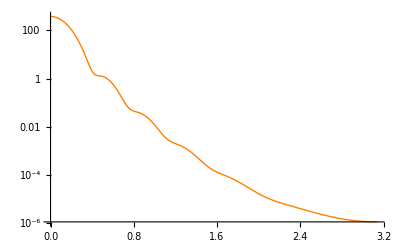

```mathematica
eik1p3=LogPlot[eik1interp3[θ],{θ,0,Pi},PlotStyle->Orange]
```

```mathematica
eik2dσdΩ[3,100]
```

{{0.,373.822},{0.01,372.674},{0.02,369.25},{0.03,363.61},{0.04,355.853},{0.05,346.113},{0.06,334.557},{0.07,321.376},{0.08,306.786},{0.09,291.018},{0.1,274.315},{0.11,256.92},{0.12,239.08},{0.13,221.032},{0.14,203.002},{0.15,185.2},{0.16,167.817},{0.17,151.02},{0.18,134.955},{0.19,119.74},{0.2,105.467},{0.21,92.2049},{0.22,79.9969},{0.23,68.8639},{0.24,58.806},{0.25,49.8051},{0.26,41.8272},{0.27,34.8252},{0.28,28.7416},{0.29,23.5109},{0.3,19.0624},{0.31,15.3223},{0.32,12.2158},{0.33,9.66895},{0.34,7.60994},{0.35,5.97056},{0.36,4.68707},{0.37,3.70083},{0.38,2.95883},{0.39,2.41382},{0.4,2.02441},{0.41,1.7549},{0.42,1.57507},{0.43,1.45978},{0.44,1.38857},{0.45,1.34521},{0.46,1.31714},{0.47,1.29505},{0.48,1.27234},{0.49,1.24466},{0.5,1.2095},{0.51,1.16577},{0.52,1.11348},{0.53,1.05339},{0.54,0.986814},{0.55,0.915356},{0.56,0.840759},{0.57,0.764762},{0.58,0.689007},{0.59,0.614966},{0.6,0.543894},{0.61,0.476808},{0.62,0.41448},{0.63,0.357442},{0.64,0.306006},{0.65,0.260284},{0.66,0.220219},{0.67,0.18561},{0.68,0.156146},{0.69,0.131434},{0.7,0.111024},{0.71,0.0944338},{0.72,0.0811716},{0.73,0.0707508},{0.74,0.062705},{0.75,0.0565989},{0.76,0.0520357},{0.77,0.0486619},{0.78,0.0461698},{0.79,0.0442981},{0.8,0.0428305},{0.81,0.0415934},{0.82,0.0404524},{0.83,0.0393082},{0.84,0.0380922},{0.85,0.036762},{0.86,0.0352969},{0.87,0.0336932},{0.88,0.0319608},{0.89,0.030119},{0.9,0.0281936},{0.91,0.026214},{0.92,0.0242109},{0.93,0.0222148},{0.94,0.0202541},{0.95,0.0183544},{0.96,0.0165376},{0.97,0.0148215},{0.98,0.0132201},{0.99,0.0117429},{1.,0.0103956},{1.01,0.00918054},{1.02,0.00809666},{1.03,0.00714029},{1.04,0.00630553},{1.05,0.00558473},{1.06,0.00496895},{1.07,0.00444841},{1.08,0.00401285},{1.09,0.0036519},{1.1,0.00335534},{1.11,0.00311336},{1.12,0.00291675},{1.13,0.002757},{1.14,0.00262646},{1.15,0.00251834},{1.16,0.00242674},{1.17,0.00234667},{1.18,0.00227398},{1.19,0.00220536},{1.2,0.00213821},{1.21,0.00207063},{1.22,0.0020013},{1.23,0.00192941},{1.24,0.00185457},{1.25,0.00177677},{1.26,0.00169624},{1.27,0.00161345},{1.28,0.00152899},{1.29,0.00144358},{1.3,0.00135794},{1.31,0.00127284},{1.32,0.00118901},{1.33,0.00110713},{1.34,0.00102781},{1.35,0.000951586},{1.36,0.000878911},{1.37,0.000810139},{1.38,0.000745534},{1.39,0.000685274},{1.4,0.00062945},{1.41,0.000578079},{1.42,0.000531109},{1.43,0.000488428},{1.44,0.000449873},{1.45,0.000415243},{1.46,0.000384303},{1.47,0.000356793},{1.48,0.000332439},{1.49,0.000310961},{1.5,0.000292072},{1.51,0.000275494},{1.52,0.000260954},{1.53,0.000248191},{1.54,0.00023696},{1.55,0.000227034},{1.56,0.000218204},{1.57,0.00021028},{1.58,0.000203095},{1.59,0.000196499},{1.6,0.000190363},{1.61,0.000184578},{1.62,0.00017905},{1.63,0.000173705},{1.64,0.000168482},{1.65,0.000163333},{1.66,0.000158225},{1.67,0.000153134},{1.68,0.000148044},{1.69,0.000142949},{1.7,0.000137848},{1.71,0.000132746},{1.72,0.000127652},{1.73,0.000122578},{1.74,0.000117538},{1.75,0.000112547},{1.76,0.000107621},{1.77,0.000102775},{1.78,0.0000980263},{1.79,0.0000933883},{1.8,0.0000888745},{1.81,0.000084497},{1.82,0.0000802663},{1.83,0.000076191},{1.84,0.0000722783},{1.85,0.0000685337},{1.86,0.0000649607},{1.87,0.0000615617},{1.88,0.0000583371},{1.89,0.0000552864},{1.9,0.0000524075},{1.91,0.0000496973},{1.92,0.0000471517},{1.93,0.0000447658},{1.94,0.0000425339},{1.95,0.0000404499},{1.96,0.0000385069},{1.97,0.000036698},{1.98,0.0000350159},{1.99,0.0000334533},{2.,0.0000320027},{2.01,0.0000306566},{2.02,0.0000294079},{2.03,0.0000282495},{2.04,0.0000271743},{2.05,0.0000261758},{2.06,0.0000252476},{2.07,0.0000243837},{2.08,0.0000235784},{2.09,0.0000228264},{2.1,0.0000221226},{2.11,0.0000214624},{2.12,0.0000208416},{2.13,0.0000202562},{2.14,0.0000197025},{2.15,0.0000191774},{2.16,0.0000186778},{2.17,0.0000182011},{2.18,0.0000177449},{2.19,0.000017307},{2.2,0.0000168856},{2.21,0.000016479},{2.22,0.0000160857},{2.23,0.0000157045},{2.24,0.0000153343},{2.25,0.0000149741},{2.26,0.0000146231},{2.27,0.0000142808},{2.28,0.0000139464},{2.29,0.0000136195},{2.3,0.0000132998},{2.31,0.0000129869},{2.32,0.0000126806},{2.33,0.0000123807},{2.34,0.000012087},{2.35,0.0000117995},{2.36,0.000011518},{2.37,0.0000112425},{2.38,0.000010973},{2.39,0.0000107094},{2.4,0.0000104517},{2.41,0.0000102},{2.42,9.9541×10^-6},{2.43,9.71413×10^-6},{2.44,9.48006×10^-6},{2.45,9.25188×10^-6},{2.46,9.02958×10^-6},{2.47,8.81313×10^-6},{2.48,8.60252×10^-6},{2.49,8.39771×10^-6},{2.5,8.19866×10^-6},{2.51,8.00534×10^-6},{2.52,7.81768×10^-6},{2.53,7.63564×10^-6},{2.54,7.45914×10^-6},{2.55,7.28812×10^-6},{2.56,7.1225×10^-6},{2.57,6.96219×10^-6},{2.58,6.80711×10^-6},{2.59,6.65716×10^-6},{2.6,6.51226×10^-6},{2.61,6.37229×10^-6},{2.62,6.23715×10^-6},{2.63,6.10675×10^-6},{2.64,5.98097×10^-6},{2.65,5.85971×10^-6},{2.66,5.74284×10^-6},{2.67,5.63027×10^-6},{2.68,5.52189×10^-6},{2.69,5.41757×10^-6},{2.7,5.31722×10^-6},{2.71,5.22072×10^-6},{2.72,5.12797×10^-6},{2.73,5.03885×10^-6},{2.74,4.95327×10^-6},{2.75,4.87111×10^-6},{2.76,4.79228×10^-6},{2.77,4.71668×10^-6},{2.78,4.64421×10^-6},{2.79,4.57479×10^-6},{2.8,4.5083×10^-6},{2.81,4.44468×10^-6},{2.82,4.38382×10^-6},{2.83,4.32566×10^-6},{2.84,4.2701×10^-6},{2.85,4.21707×10^-6},{2.86,4.16649×10^-6},{2.87,4.1183×10^-6},{2.88,4.07243×10^-6},{2.89,4.0288×10^-6},{2.9,3.98736×10^-6},{2.91,3.94804×10^-6},{2.92,3.91079×10^-6},{2.93,3.87556×10^-6},{2.94,3.84228×10^-6},{2.95,3.81092×10^-6},{2.96,3.78143×10^-6},{2.97,3.75376×10^-6},{2.98,3.72787×10^-6},{2.99,3.70372×10^-6},{3.,3.68128×10^-6},{3.01,3.66052×10^-6},{3.02,3.64139×10^-6},{3.03,3.62389×10^-6},{3.04,3.60797×10^-6},{3.05,3.59362×10^-6},{3.06,3.58081×10^-6},{3.07,3.56953×10^-6},{3.08,3.55975×10^-6},{3.09,3.55147×10^-6},{3.1,3.54466×10^-6},{3.11,3.53933×10^-6},{3.12,3.53547×10^-6},{3.13,3.53305×10^-6},{3.14,3.5321×10^-6}}

```mathematica
eik2interp3=Interpolation[%];
```

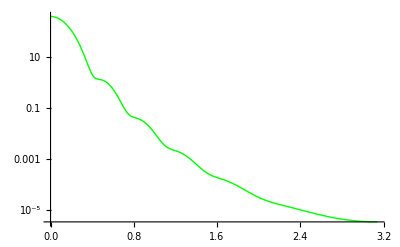

```mathematica
eik2p3=LogPlot[eik2interp3[θ],{θ,0,Pi},PlotStyle->Green]
```

```mathematica
eik3dσdΩ[3,100]
```

{{0.,373.882},{0.01,372.735},{0.02,369.312},{0.03,363.674},{0.04,355.921},{0.05,346.185},{0.06,334.632},{0.07,321.456},{0.08,306.871},{0.09,291.108},{0.1,274.408},{0.11,257.017},{0.12,239.18},{0.13,221.134},{0.14,203.105},{0.15,185.304},{0.16,167.919},{0.17,151.121},{0.18,135.053},{0.19,119.833},{0.2,105.556},{0.21,92.2879},{0.22,80.0736},{0.23,68.9337},{0.24,58.8686},{0.25,49.8603},{0.26,41.8749},{0.27,34.8655},{0.28,28.7747},{0.29,23.5372},{0.3,19.0824},{0.31,15.3365},{0.32,12.2248},{0.33,9.6733},{0.34,7.61029},{0.35,5.96753},{0.36,4.68126},{0.37,3.69283},{0.38,2.94915},{0.39,2.40294},{0.4,2.01275},{0.41,1.74283},{0.42,1.56289},{0.43,1.44773},{0.44,1.37685},{0.45,1.33395},{0.46,1.30644},{0.47,1.28496},{0.48,1.26289},{0.49,1.23585},{0.5,1.2013},{0.51,1.15816},{0.52,1.1064},{0.53,1.0468},{0.54,0.98066},{0.55,0.909591},{0.56,0.835335},{0.57,0.75964},{0.58,0.684151},{0.59,0.610346},{0.6,0.539485},{0.61,0.472591},{0.62,0.410439},{0.63,0.353565},{0.64,0.302284},{0.65,0.25671},{0.66,0.216785},{0.67,0.18231},{0.68,0.152974},{0.69,0.128381},{0.7,0.108083},{0.71,0.0915958},{0.72,0.078427},{0.73,0.0680893},{0.74,0.0601163},{0.75,0.0540727},{0.76,0.049562},{0.77,0.0462313},{0.78,0.0437742},{0.79,0.0419304},{0.8,0.0404853},{0.81,0.0392669},{0.82,0.0381424},{0.83,0.0370144},{0.84,0.035816},{0.85,0.0345062},{0.86,0.0330658},{0.87,0.0314922},{0.88,0.0297962},{0.89,0.0279978},{0.9,0.026123},{0.91,0.0242013},{0.92,0.0222633},{0.93,0.020339},{0.94,0.0184561},{0.95,0.0166393},{0.96,0.0149096},{0.97,0.0132837},{0.98,0.0117744},{0.99,0.0103901},{1.,0.00913545},{1.01,0.00801148},{1.02,0.00701622},{1.03,0.0061451},{1.04,0.00539141},{1.05,0.00474686},{1.06,0.00420201},{1.07,0.00374671},{1.08,0.0033705},{1.09,0.00306293},{1.1,0.00281383},{1.11,0.00261357},{1.12,0.00245319},{1.13,0.00232455},{1.14,0.00222041},{1.15,0.00213444},{1.16,0.00206126},{1.17,0.00199639},{1.18,0.00193622},{1.19,0.00187793},{1.2,0.00181942},{1.21,0.00175923},{1.22,0.00169647},{1.23,0.00163069},{1.24,0.00156184},{1.25,0.00149014},{1.26,0.00141608},{1.27,0.00134025},{1.28,0.0012634},{1.29,0.00118628},{1.3,0.00110967},{1.31,0.00103431},{1.32,0.000960901},{1.33,0.000890047},{1.34,0.000822281},{1.35,0.000758034},{1.36,0.000697641},{1.37,0.000641336},{1.38,0.000589264},{1.39,0.00054148},{1.4,0.000497961},{1.41,0.000458616},{1.42,0.000423296},{1.43,0.000391801},{1.44,0.000363898},{1.45,0.000339322},{1.46,0.000317791},{1.47,0.000299012},{1.48,0.000282692},{1.49,0.000268539},{1.5,0.000256272},{1.51,0.000245621},{1.52,0.000236336},{1.53,0.000228186},{1.54,0.00022096},{1.55,0.00021447},{1.56,0.000208552},{1.57,0.000203063},{1.58,0.000197881},{1.59,0.000192905},{1.6,0.000188055},{1.61,0.000183266},{1.62,0.000178491},{1.63,0.000173694},{1.64,0.000168855},{1.65,0.000163963},{1.66,0.000159015},{1.67,0.000154015},{1.68,0.000148975},{1.69,0.000143908},{1.7,0.000138832},{1.71,0.000133767},{1.72,0.000128734},{1.73,0.000123753},{1.74,0.000118844},{1.75,0.000114026},{1.76,0.000109317},{1.77,0.000104734},{1.78,0.000100289},{1.79,0.0000959952},{1.8,0.0000918617},{1.81,0.0000878961},{1.82,0.0000841038},{1.83,0.0000804882},{1.84,0.0000770507},{1.85,0.0000737911},{1.86,0.0000707075},{1.87,0.0000677969},{1.88,0.0000650548},{1.89,0.0000624759},{1.9,0.0000600539},{1.91,0.000057782},{1.92,0.0000556527},{1.93,0.0000536585},{1.94,0.0000517912},{1.95,0.0000500429},{1.96,0.0000484056},{1.97,0.0000468713},{1.98,0.0000454322},{1.99,0.000044081},{2.,0.0000428103},{2.01,0.0000416134},{2.02,0.0000404838},{2.03,0.0000394155},{2.04,0.0000384028},{2.05,0.0000374405},{2.06,0.0000365238},{2.07,0.0000356482},{2.08,0.0000348099},{2.09,0.0000340051},{2.1,0.0000332308},{2.11,0.0000324839},{2.12,0.0000317619},{2.13,0.0000310626},{2.14,0.000030384},{2.15,0.0000297244},{2.16,0.0000290822},{2.17,0.0000284563},{2.18,0.0000278456},{2.19,0.0000272491},{2.2,0.0000266661},{2.21,0.000026096},{2.22,0.0000255382},{2.23,0.0000249923},{2.24,0.0000244579},{2.25,0.0000239349},{2.26,0.000023423},{2.27,0.0000229221},{2.28,0.0000224319},{2.29,0.0000219525},{2.3,0.0000214836},{2.31,0.0000210254},{2.32,0.0000205776},{2.33,0.0000201403},{2.34,0.0000197135},{2.35,0.000019297},{2.36,0.0000188908},{2.37,0.0000184948},{2.38,0.000018109},{2.39,0.0000177334},{2.4,0.0000173677},{2.41,0.0000170119},{2.42,0.000016666},{2.43,0.0000163297},{2.44,0.0000160031},{2.45,0.0000156858},{2.46,0.0000153778},{2.47,0.0000150789},{2.48,0.0000147891},{2.49,0.000014508},{2.5,0.0000142355},{2.51,0.0000139716},{2.52,0.0000137159},{2.53,0.0000134683},{2.54,0.0000132286},{2.55,0.0000129966},{2.56,0.0000127722},{2.57,0.0000125551},{2.58,0.0000123452},{2.59,0.0000121423},{2.6,0.0000119462},{2.61,0.0000117566},{2.62,0.0000115736},{2.63,0.0000113967},{2.64,0.000011226},{2.65,0.0000110612},{2.66,0.0000109021},{2.67,0.0000107485},{2.68,0.0000106004},{2.69,0.0000104576},{2.7,0.0000103198},{2.71,0.0000101871},{2.72,0.0000100591},{2.73,9.93583×10^-6},{2.74,9.81711×10^-6},{2.75,9.7028×10^-6},{2.76,9.59278×10^-6},{2.77,9.48693×10^-6},{2.78,9.38514×10^-6},{2.79,9.2873×10^-6},{2.8,9.19329×10^-6},{2.81,9.10302×10^-6},{2.82,9.01638×10^-6},{2.83,8.93329×10^-6},{2.84,8.85365×10^-6},{2.85,8.77737×10^-6},{2.86,8.70438×10^-6},{2.87,8.63459×10^-6},{2.88,8.56793×10^-6},{2.89,8.50432×10^-6},{2.9,8.44371×10^-6},{2.91,8.38602×10^-6},{2.92,8.33119×10^-6},{2.93,8.27917×10^-6},{2.94,8.22989×10^-6},{2.95,8.18332×10^-6},{2.96,8.1394×10^-6},{2.97,8.09808×10^-6},{2.98,8.05933×10^-6},{2.99,8.02309×10^-6},{3.,7.98935×10^-6},{3.01,7.95805×10^-6},{3.02,7.92917×10^-6},{3.03,7.90268×10^-6},{3.04,7.87855×10^-6},{3.05,7.85676×10^-6},{3.06,7.83728×10^-6},{3.07,7.8201×10^-6},{3.08,7.8052×10^-6},{3.09,7.79256×10^-6},{3.1,7.78217×10^-6},{3.11,7.77403×10^-6},{3.12,7.76811×10^-6},{3.13,7.76442×10^-6},{3.14,7.76296×10^-6}}

```mathematica
eik3interp3=Interpolation[%];
```

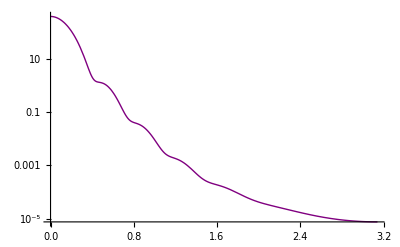

```mathematica
eik3p3=LogPlot[eik3interp3[θ],{θ,0,Pi},PlotStyle->Purple]
```

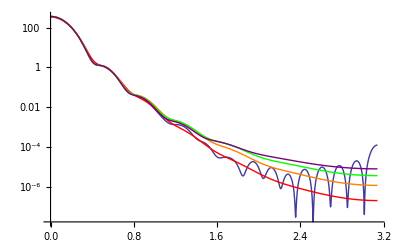

```mathematica
Show[p3,eik0p3,eik1p3,eik2p3,eik3p3,PlotRange->Automatic]
```

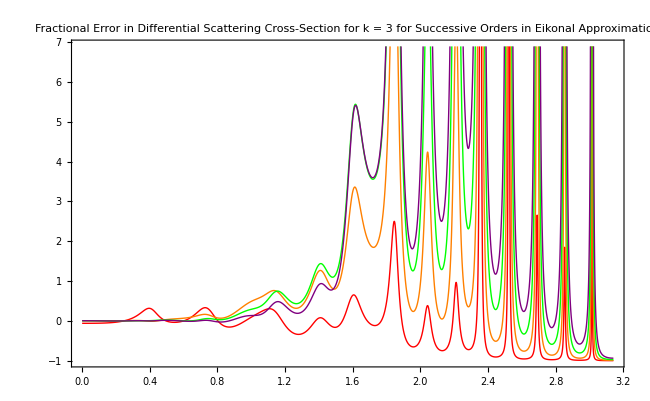

```mathematica
Plot[{(eik0interp3[θ]-temp[θ])/temp[θ],(eik1interp3[θ]-temp[θ])/temp[θ],(eik2interp3[θ]-temp[θ])/temp[θ],(eik3interp3[θ]-temp[θ])/temp[θ]},{θ,0,Pi},PlotLabel->"Fractional Error in Differential Scattering Cross-Section
for k = 3 for Successive Orders in Eikonal Approximation",PlotStyle->{Red,Orange,Green,Purple},PlotLegend->{"Zeroth Order Eikonal","First Order Eikonal","Second Order Eikonal","Third Order Eikonal"},AxesLabel->{θ},LegendPosition->{.85,-0.2},LegendSize->{.9,0.4},ImageSize->650,Frame->True]
```

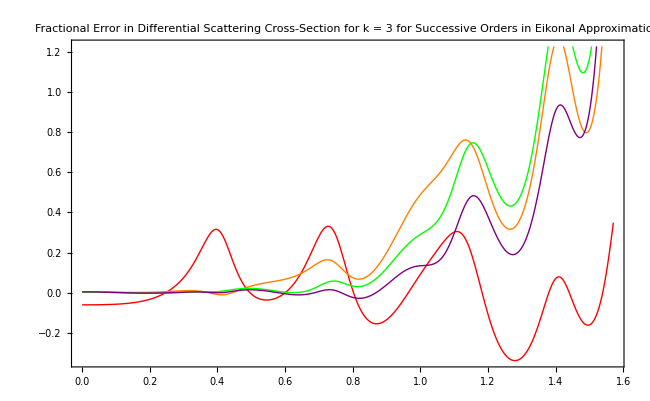

```mathematica
Plot[{(eik0interp3[θ]-temp[θ])/temp[θ],(eik1interp3[θ]-temp[θ])/temp[θ],(eik2interp3[θ]-temp[θ])/temp[θ],(eik3interp3[θ]-temp[θ])/temp[θ]},{θ,0,Pi/2},PlotLabel->"Fractional Error in Differential Scattering Cross-Section
for k = 3 for Successive Orders in Eikonal Approximation",AxesLabel->{θ},PlotStyle->{Red,Orange,Green,Purple},PlotLegend->{"Zeroth Order Eikonal","First Order Eikonal","Second Order Eikonal","Third Order Eikonal"},LegendPosition->{.85,-0.2},LegendSize->{.9,0.4},ImageSize->650,Frame->True]
```

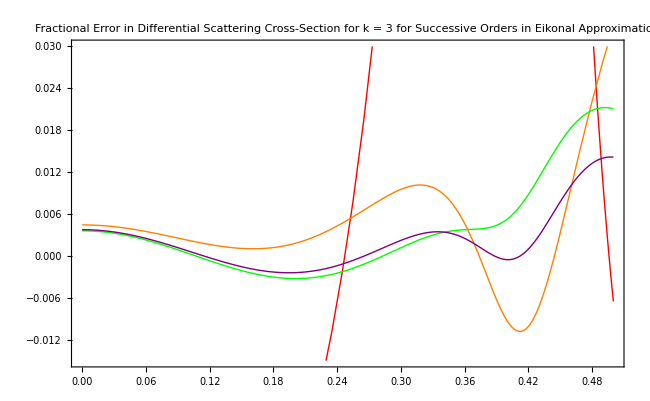

```mathematica
Plot[{(eik0interp3[θ]-temp[θ])/temp[θ],(eik1interp3[θ]-temp[θ])/temp[θ],(eik2interp3[θ]-temp[θ])/temp[θ],(eik3interp3[θ]-temp[θ])/temp[θ]},{θ,0,.5},PlotRange->{-.015,.03},PlotLabel->"Fractional Error in Differential Scattering Cross-Section
for k = 3 for Successive Orders in Eikonal Approximation",AxesLabel->{θ},PlotStyle->{Red,Orange,Green,Purple},PlotLegend->{"Zeroth Order Eikonal","First Order Eikonal","Second Order Eikonal","Third Order Eikonal"},LegendPosition->{.85,-0.2},LegendSize->{.9,0.4},ImageSize->650,Frame->True]
```

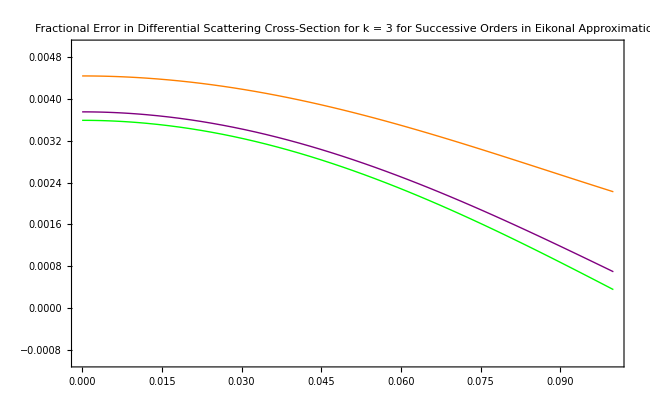

```mathematica
Plot[{(eik0interp3[θ]-temp[θ])/temp[θ],(eik1interp3[θ]-temp[θ])/temp[θ],(eik2interp3[θ]-temp[θ])/temp[θ],(eik3interp3[θ]-temp[θ])/temp[θ]},{θ,0,.1},PlotRange->{-0.001,0.005},PlotLabel->"Fractional Error in Differential Scattering Cross-Section
for k = 3 for Successive Orders in Eikonal Approximation",AxesLabel->{θ},PlotStyle->{Red,Orange,Green,Purple},PlotLegend->{"Zeroth Order Eikonal","First Order Eikonal","Second Order Eikonal","Third Order Eikonal"},LegendPosition->{.85,-0.2},LegendSize->{.9,0.4},ImageSize->650,Frame->True]
```

As can be seen from the above four graphs, the fractional error in general becomes smaller as we go to higher orders in the eikonal series. Furthermore, the range of validity in θ increases with increasing order. The only exception to these results can be seen upon close inspection of the forward scattering direction. In the forward direction, the approximation to second order actually has a smaller fractional error than the approximation to third order.

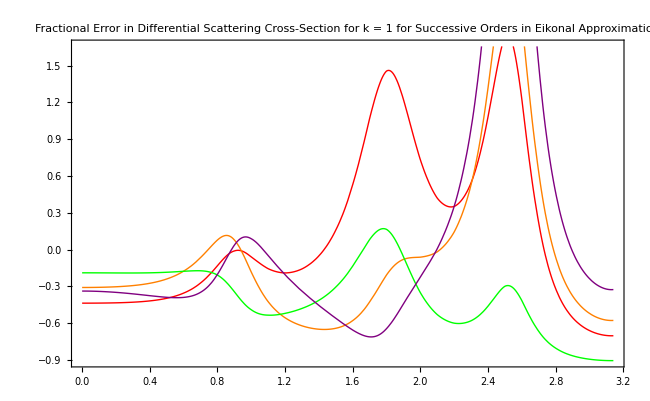

```mathematica
Plot[{(eik0interp1[θ]-interp1[θ])/interp1[θ],(eik1interp1[θ]-interp1[θ])/interp1[θ],(eik2interp1[θ]-interp1[θ])/interp1[θ],(eik3interp1[θ]-interp1[θ])/interp1[θ]},{θ,0,Pi},PlotLabel->"Fractional Error in Differential Scattering Cross-Section
for k = 1 for Successive Orders in Eikonal Approximation",PlotStyle->{Red,Orange,Green,Purple},PlotLegend->{"Zeroth Order Eikonal","First Order Eikonal","Second Order Eikonal","Third Order Eikonal"},AxesLabel->{θ},LegendPosition->{.85,-0.2},LegendSize->{.9,0.4},ImageSize->650,Frame->True]
```